First we define our system of equations and also partition a piece for solutions of a truncated system

```mathematica
alp = Table[Symbol["a" <> ToString@i],{i,1,12}];
bet = Table[Symbol["b" <> ToString@i],{i,1,12}];
ns = Table[Symbol["n" <> ToString@i],{i,1,12}];
diffs = Flatten[
{Table[-Abs@alp[[i]]*ns[[i]][t],{i,1,1}],(*Uncoupled stuff*)
-(Abs@alp[[11]]+Abs@alp[[2]])*ns[[2]][t] +Abs@bet[[2]]*ns[[Length@ns]][t] + Abs@alp[[1]]*ns[[1]][t],
Table[ Abs@bet[[i]]*ns[[Length[ns]]][t] - Abs@alp[[i]]*ns[[i]][t],{i,3,10}],(*To serum stuff*)
Abs@alp[[Length[alp]-1]]* ns[[2]][t],(*Waste stuff*)
Sum[Abs@alp[[i]]*ns[[i]][t], {i,2,10}] - Sum[Abs@bet[[i]],{i,2,10}]*ns[[Length[ns]]][t]}];(*my man the serum*)
derv = Table[ns[[i]]'[t],{i,1,12}];
derv2 = Delete[derv,{7}]
system = Table[derv[[i]] == diffs[[i]],{i,1,Length[derv]}];
alp2 = Delete[alp,{7}];
bet2 = Delete[bet,{7}];
ns2 = Delete[ns,{7}];
diffs2 = Flatten[
{Table[-Abs@alp2[[i]]*ns2[[i]][t],{i,1,1}],(*Uncoupled stuff*)
-(Abs@alp2[[10]]+Abs@alp2[[2]])*ns2[[2]][t] +Abs@bet2[[2]]*ns2[[Length@ns2]][t] + Abs@alp2[[1]]*ns2[[1]][t],
Table[ Abs@bet2[[i]]*ns2[[Length[ns2]]][t] - Abs@alp2[[i]]*ns2[[i]][t],{i,3,9}],(*To serum stuff*)
Abs@alp2[[Length[alp2]-1]]* ns2[[2]][t],(*Waste stuff*)
Sum[Abs@alp2[[i]]*ns2[[i]][t], {i,2,9}] - Sum[Abs@bet2[[i]],{i,2,9}]*ns2[[Length[ns2]]][t]}];(*my man the serum*)
system2 = Table[derv2[[i]] == diffs2[[i]],{i,1,Length[derv2]}];


{system//TableForm,approxsystem//TableForm}
{system2//TableForm,approxsystem2//TableForm}
```

{n1'[t],n2'[t],n3'[t],n4'[t],n5'[t],n6'[t],n8'[t],n9'[t],n10'[t],n11'[t],n12'[t]}

{n1'[t]==-Abs[a1] n1[t]
n2'[t]==Abs[a1] n1[t]+Abs[b2] n12[t]+(-Abs[a11]-Abs[a2]) n2[t]
n3'[t]==Abs[b3] n12[t]-Abs[a3] n3[t]
n4'[t]==Abs[b4] n12[t]-Abs[a4] n4[t]
n5'[t]==Abs[b5] n12[t]-Abs[a5] n5[t]
n6'[t]==Abs[b6] n12[t]-Abs[a6] n6[t]
n7'[t]==Abs[b7] n12[t]-Abs[a7] n7[t]
n8'[t]==Abs[b8] n12[t]-Abs[a8] n8[t]
n9'[t]==Abs[b9] n12[t]-Abs[a9] n9[t]
n10'[t]==-Abs[a10] n10[t]+Abs[b10] n12[t]
n11'[t]==Abs[a11] n2[t]
n12'[t]==Abs[a10] n10[t]-(Abs[b10]+Abs[b2]+Abs[b3]+Abs[b4]+Abs[b5]+Abs[b6]+Abs[b7]+Abs[b8]+Abs[b9]) n12[t]+Abs[a2] n2[t]+Abs[a3] n3[t]+Abs[a4] n4[t]+Abs[a5] n5[t]+Abs[a6] n6[t]+Abs[a7] n7[t]+Abs[a8] n8[t]+Abs[a9] n9[t],approxsystem}

{n1'[t]==-Abs[a1] n1[t]
n2'[t]==Abs[a1] n1[t]+Abs[b2] n12[t]+(-Abs[a11]-Abs[a2]) n2[t]
n3'[t]==Abs[b3] n12[t]-Abs[a3] n3[t]
n4'[t]==Abs[b4] n12[t]-Abs[a4] n4[t]
n5'[t]==Abs[b5] n12[t]-Abs[a5] n5[t]
n6'[t]==Abs[b6] n12[t]-Abs[a6] n6[t]
n8'[t]==Abs[b8] n12[t]-Abs[a8] n8[t]
n9'[t]==Abs[b9] n12[t]-Abs[a9] n9[t]
n10'[t]==-Abs[a10] n10[t]+Abs[b10] n12[t]
n11'[t]==Abs[a11] n2[t]
n12'[t]==Abs[a10] n10[t]-(Abs[b10]+Abs[b2]+Abs[b3]+Abs[b4]+Abs[b5]+Abs[b6]+Abs[b8]+Abs[b9]) n12[t]+Abs[a2] n2[t]+Abs[a3] n3[t]+Abs[a4] n4[t]+Abs[a5] n5[t]+Abs[a6] n6[t]+Abs[a8] n8[t]+Abs[a9] n9[t],n1'[t]==-Abs[a1] n1[t]
n2'[t]==Abs[a1] n1[t]+Abs[b2] n12[t]+(-Abs[a11]-Abs[a2]) n2[t]
n3'[t]==Abs[b3] n12[t]-Abs[a3] n3[t]
n4'[t]==Abs[b4] n12[t]-Abs[a4] n4[t]
n5'[t]==Abs[b5] n12[t]-Abs[a5] n5[t]
n6'[t]==Abs[b6] n12[t]-Abs[a6] n6[t]
n8'[t]==Abs[b8] n12[t]-Abs[a8] n8[t]
n9'[t]==Abs[b9] n12[t]-Abs[a9] n9[t]
n10'[t]==-Abs[a10] n10[t]+Abs[b10] n12[t]
n11'[t]==Abs[a11] n2[t]
n12'[t]==0}

```mathematica
approxsystem2={n1'[t]==-Abs[a1] n1[t],n2'[t]==Abs[a1] n1[t]+Abs[b2] n12[t]+(-Abs[a11]-Abs[a2]) n2[t],n3'[t]==Abs[b3] n12[t]-Abs[a3] n3[t],n4'[t]==Abs[b4] n12[t]-Abs[a4] n4[t],n5'[t]==Abs[b5] n12[t]-Abs[a5] n5[t],n6'[t]==Abs[b6] n12[t]-Abs[a6] n6[t],n8'[t]==Abs[b8] n12[t]-Abs[a8] n8[t],n9'[t]==Abs[b9] n12[t]-Abs[a9] n9[t],n10'[t]==-Abs[a10] n10[t]+Abs[b10] n12[t],n11'[t]==Abs[a11] n2[t],n12'[t]==0}
```

{n1'[t]==-Abs[a1] n1[t],n2'[t]==Abs[a1] n1[t]+Abs[b2] n12[t]+(-Abs[a11]-Abs[a2]) n2[t],n3'[t]==Abs[b3] n12[t]-Abs[a3] n3[t],n4'[t]==Abs[b4] n12[t]-Abs[a4] n4[t],n5'[t]==Abs[b5] n12[t]-Abs[a5] n5[t],n6'[t]==Abs[b6] n12[t]-Abs[a6] n6[t],n8'[t]==Abs[b8] n12[t]-Abs[a8] n8[t],n9'[t]==Abs[b9] n12[t]-Abs[a9] n9[t],n10'[t]==-Abs[a10] n10[t]+Abs[b10] n12[t],n11'[t]==Abs[a11] n2[t],n12'[t]==0}

Now we prepare vectors of initial conditions as well as their counterparts.

```mathematica
Riffle[approxsystem2,ic2]
```

Riffle::list: List expected at position 1 in Riffle[approxsystem2, {n1[0] == 11.2338, n2[0] == 7.83625, n3[0] == 9.60897, n4[0] == 9.53241, n5[0] == 4.35791, n6[0] == 7.76052, n8[0] == 8.5161, n9[0] == 9.42423, n10[0] == 5.79047, n11[0] == 0, n12[0] == 6.85681}].

Riffle[approxsystem2,{n1[0]==11.2338,n2[0]==7.83625,n3[0]==9.60897,n4[0]==9.53241,n5[0]==4.35791,n6[0]==7.76052,n8[0]==8.5161,n9[0]==9.42423,n10[0]==5.79047,n11[0]==0,n12[0]==6.85681}]

```mathematica
initcond = {11.233753496899364,7.836250157862164,9.608970201701684,9.53240652539371,
4.357914923821371,7.7605185248645085,11.597172303950263,8.516102143592978,9.42422531532899,
5.790466859094781,0,6.856809541483823};
initcond2 = Delete[initcond,{7}];
ic = Table[ns[[i]][0] ==initcond[[i]],{i,1,Length@initcond}]
ic2 = Table[ns2[[i]][0]==initcond2[[i]],{i,1,Length@initcond2}]
points = Range[0.001,12,.3]; (*points to fit with*)
```

{n1[0]==11.2338,n2[0]==7.83625,n3[0]==9.60897,n4[0]==9.53241,n5[0]==4.35791,n6[0]==7.76052,n7[0]==11.5972,n8[0]==8.5161,n9[0]==9.42423,n10[0]==5.79047,n11[0]==0,n12[0]==6.85681}

{n1[0]==11.2338,n2[0]==7.83625,n3[0]==9.60897,n4[0]==9.53241,n5[0]==4.35791,n6[0]==7.76052,n8[0]==8.5161,n9[0]==9.42423,n10[0]==5.79047,n11[0]==0,n12[0]==6.85681}

```mathematica
sol = ParametricNDSolveValue[
Riffle[system,ic],
Table[ns[[i]],{i,1,12}],
{t,0,15},
Flatten[{
Table[alp[[i]],{i,1,11}],
Table[bet[[i]],{i,2,10}]
}],
Method->"LSODA"]; (*set up equations to optimize*)


sol2 = ParametricNDSolveValue[
Riffle[system2,ic2],
Table[ns2[[i]],{i,1,11}],
{t,0,15},
Flatten[{
Table[alp2[[i]],{i,1,10}],
Table[bet2[[i]],{i,2,9}]
}],
Method->"LSODA"]; (*set up equations to optimize*)
apsol2 =  ParametricNDSolveValue[
Riffle[approxsystem2,ic2],
Table[ns2[[i]],{i,1,11}],
{t,0,15},
params2,
Method->"LSODA"]; (*set up equations to optimize*)
```

```mathematica
points = Range[0.001,12,.3];
ordinates=With[{a1=0.12512044723935,a2=0.2453021,a3=0.7491892366497901,a4=0.44118386223923545,a5=0.17193008586682357,a6=0.922720059201386,a7=0.7124062074680186,a8=0.5898966317547063,a9 = 0.8498145306514904, a10 =0.7778254794939592,a11=0.007256062876177221,b2=0.240343, b3=0.7902230762443223,b4=0.31166228728883012,b5=0.06655575840953443,b6=0.9795814487355847,b7=0.6580558294204786,b8=0.599771396211936,b9=0.6398638788598377,b10=0.8907779882884594}
,Through[sol[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,b2,b3,b4,b5,b6,b7,b8,b9,b10][points],List]];
ordinates = Delete[ordinates,{7}];
data = ordinates+RandomVariate[NormalDistribution[0,.25],Dimensions[ordinates]];
transformedData={ConstantArray[Range@Length[ordinates],Length[points]]//Transpose,ConstantArray[points,Length[ordinates]],data}~Flatten~{{2,3},{1}};
lessData = DeleteCases[transformedData,{Length@ns2 - 1,__}]
```

```mathematica
other = Abs[initcond + RandomVariate[NormalDistribution[0,.25],Dimensions[initcond]]]
```

{11.3519,7.4336,9.6796,9.51057,4.01405,7.44761,11.5562,8.02349,9.70967,5.74599,0.17233,6.72226}

```mathematica
DataRandomSampler[regions_,equations_,nump_]:= 
(*Grab random elements from the data, sort and partition it correctly for use in the model fititng*)
Table[
Sort[
RandomSample[
Partition[regions,Length[regions]/equations][[i]],nump],
#1[[2]]<#2[[2]]&],
{i,1,equations}]~Flatten~{1,2}


EqualDataRandomSample[regions_,equations_,nump_]:= 
(*Need to have evenly spaced data, sampled randomly, which apparently is way easier to do than I thought before*)
SortBy[
RandomSample[
Transpose[Partition[regions,Length[regions]/equations]],nump]~Flatten~{1,2}, First]
ChooseData[regions_,equations_,nump_]:= 
SortBy[
Transpose[Partition[regions,Length[regions]/equations]][[nump]]~Flatten~{1,2}, First]

ModelSys[args_][i_,t_]:=Through[(sol@@args)[t],List][[i]]/;
And@@NumericQ/@Flatten[{args,i,t}];

ApModelSys[args_][i_,t_]:=Through[(apsol@@args)[t],List][[i]]/;
And@@NumericQ/@Flatten[{args,i,t}];

ModelSys2[args_][i_,t_]:=Through[(sol2@@args)[t],List][[i]]/;
And@@NumericQ/@Flatten[{args,i,t}];

ApModelSys2[args_][i_,t_]:=Through[(apsol2@@args)[t],List][[i]]/;
And@@NumericQ/@Flatten[{args,i,t}];

params = Flatten[{Table[alp[[i]],{i,1,11}],Table[bet[[i]],{i,2,10}]}];
params2 = Delete[params,{{7},{17}}];
```

```mathematica
params2
```

{a1,a2,a3,a4,a5,a6,a8,a9,a10,a11,b2,b3,b4,b5,b6,b8,b9,b10}

```mathematica
fitdata =ChooseData[lessData,Length@ns2-1,{2,6,10,40}](*EqualDataRandomSample[lessData,Length@ns-1,4];*)
fit3=NonlinearModelFit[fitdata,
ModelSys2[params2][i,t],
params2,{i,t},
Method->"LevenbergMarquardt",
PrecisionGoal->∞,
MaxIterations->600];
```

{{1,0.301,11.0907},{1,1.501,9.35086},{1,2.701,8.07505},{1,11.701,2.68466},{2,0.301,8.29625},{2,1.501,9.95402},{2,2.701,10.7909},{2,11.701,11.2299},{3,0.301,9.20431},{3,1.501,9.60585},{3,2.701,9.24599},{3,11.701,10.2832},{4,0.301,9.04849},{4,1.501,7.98879},{4,2.701,7.09703},{4,11.701,6.80965},{5,0.301,4.1308},{5,1.501,4.57574},{5,2.701,3.85101},{5,11.701,3.90038},{6,0.301,7.99609},{6,1.501,9.04043},{6,2.701,9.11793},{6,11.701,10.3919},{7,0.301,8.48814},{7,1.501,8.60375},{7,2.701,9.25466},{7,11.701,10.7984},{8,0.301,8.70836},{8,1.501,7.57613},{8,2.701,6.9422},{8,11.701,7.51646},{9,0.301,6.48546},{9,1.501,8.78421},{9,2.701,9.77692},{9,11.701,10.8233},{11,0.301,9.07711},{11,1.501,9.14854},{11,2.701,9.08991},{11,11.701,10.0965}}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

```mathematica
ic = Table[ns[[i]][0] ==initcond[[i]],{i,1,Length@initcond}]
```

{n1[0]==11.2338,n2[0]==7.83625,n3[0]==9.60897,n4[0]==9.53241,n5[0]==4.35791,n6[0]==7.76052,n7[0]==11.5972,n8[0]==8.5161,n9[0]==9.42423,n10[0]==5.79047,n11[0]==0,n12[0]==6.85681}

```mathematica
listgrabs = {{2,4,8,30},{2,4,6,8,30},{2,4,6,8,12,14,30},{2,4,6,8,12,14,16,30}}
ParamEstimates =Table[{},{j,1,Length@listgrabs}]
points = Range[0.001,12,.3];
ic = Table[ns[[i]][0] ==initcond[[i]],{i,1,Length@initcond}];
sol = ParametricNDSolveValue[
Riffle[system,ic],
Table[ns[[i]],{i,1,12}],
{t,0,15},
Flatten[{
Table[alp[[i]],{i,1,11}],
Table[bet[[i]],{i,2,10}]
}],
Method->"LSODA"]; (*set up equations to optimize*)
Do[
count = 1;
dump = {};
While[count<501,
other = Abs[Delete[initcond,{7}] + RandomVariate[NormalDistribution[0,.25],Dimensions[Delete[initcond,{7}]]]];

 (*Also add noise to the inital conditions of the parameters*)
ic2 = Table[ns2[[i]][0]==other[[i]],{i,1,Length@other}];

sol2 = ParametricNDSolveValue[
Riffle[system2,ic2],
Table[ns2[[i]],{i,1,11}],
{t,0,15},
Flatten[{
Table[alp2[[i]],{i,1,10}],
Table[bet2[[i]],{i,2,9}]
}],
Method->"LSODA"]; (*set up equations to optimize*)

apsol2 =  ParametricNDSolveValue[
Riffle[approxsystem2,ic2],
Table[ns2[[i]],{i,1,11}],
{t,0,15},
params2,
Method->"LSODA"]; (*set up equations to optimize*)

ordinates=With[{a1=0.12512044723935,
a2=0.2453021,
a3=0.7491892366497901,
a4=0.44118386223923545,
a5=0.17193008586682357,
a6=0.922720059201386,
a7=0.7124062074680186,
a8=0.5898966317547063,
a9 = 0.8498145306514904,
 a10 =0.7778254794939592,
a11=0.007256062876177221,
b2=0.240343, 
b3=0.7902230762443223,
b4=0.31166228728883012,
b5=0.06655575840953443,
b6=0.9795814487355847,
b7=0.6580558294204786,
b8=0.599771396211936,
b9=0.6398638788598377,
b10=0.8907779882884594}
,Through[sol[a1,a2,a3,a4,a5,a6,a7,a8,a9,a10,a11,b2,b3,b4,b5,b6,b7,b8,b9,b10][points],List]
];

ordinates = Delete[ordinates,{7}]; (*get rid of data set we're pretending we don't know about*)
data = ordinates+RandomVariate[NormalDistribution[0,.25],Dimensions[ordinates]];
transformedData={ConstantArray[Range@Length[ordinates],Length[points]]//Transpose,ConstantArray[points,Length[ordinates]],data}~Flatten~{{2,3},{1}};
lessData = DeleteCases[transformedData,{Length@ns2 - 1,__}];

fitdata =ChooseData[lessData,Length@ns2-1,listgrabs[[k]]];

apfit2 = NonlinearModelFit[
fitdata,
ApModelSys2[params2][i,t],
params2,{i,t},
Method->"LevenbergMarquardt",
PrecisionGoal->∞,
MaxIterations->600
];
guess =Riffle[params2,Table[
If[
apfit2["BestFitParameters"][[i,2]] >-0.1 && apfit2["BestFitParameters"][[i,2]] <1.5,
apfit2["BestFitParameters"][[i,2]],
.5]
 ,{i,1,Length@params2}]]~Partition~2;
fit2 = NonlinearModelFit[
fitdata,
ModelSys2[params2][i,t],
guess,{i,t},
Method->"LevenbergMarquardt",
PrecisionGoal->∞,
MaxIterations->600
];

AppendTo[ParamEstimates[[k]],Table[fit2["BestFitParameters"][[i,2]],{i,1,Length@params2}]];
count++
];
Print[k];
,{k,1,Length@listgrabs}]
```

{{2,4,8,30},{2,4,6,8,30},{2,4,6,8,12,14,30},{2,4,6,8,12,14,16,30}}

{{},{},{},{}}

NonlinearModelFit::sszero: The step size in the search has become less than the tolerance prescribed by the PrecisionGoal option, but the gradient is larger than the tolerance specified by the AccuracyGoal option. There is a possibility that the method has stalled at a point that is not a local minimum.

General::stop: Further output of NonlinearModelFit :: sszero will be suppressed during this calculation.

NonlinearModelFit::cvmit: Failed to converge to the requested accuracy or precision within 600 iterations.

General::stop: Further output of NonlinearModelFit :: cvmit will be suppressed during this calculation.

1

2

3

4

```mathematica
Filter[array_]:=
Table[
If[
array[[i]] > Mean[array] +  2*StandardDeviation[array],
{i},
Unevaluated[Sequence[]]],
{i,1,Length@array}];
size[array1_,array2_]:=
If[Length@array1 == Length@array2,
Unevaluated[Sequence[]],
If[Length@array1 > Length@array2,
Return[Delete[array2,Table[{i},{i,Length@array1,Length@array2}]]],
Return[Delete[array1,Table[{i},{i,Length@array2,Length@array1}]]]
]
]
size[array1_,array2_]:=
If[Length@array1 == Length@array2,
Unevaluated[Sequence[]],
If[Length@array1 > Length@array2,
Return[Delete[array2,Table[{i},{i,Length@array1,Length@array2}]]],
Return[Delete[array1,Table[{i},{i,Length@array2,Length@array1}]]]
]
]
Needs["MultivariateStatistics`"]
Plotter[array1_,array2_,label1_,label2_]:= 
Show[
ListPlot[Transpose@{array1,array2}],
Graphics[{Thick,Red,Opacity[.4],EllipsoidQuantile[Transpose@{array1,array2},.95]}],
Graphics[{
Style[Text["α =",Scaled[{0.1,0.9}]],FontSize->16],
Style[Text[ToString@Round[Mean[array1],10.^-3],Scaled[{0.2,0.9}]],FontSize->16],
Style[Text["±",Scaled[{0.3,0.9}]],FontSize->16],
Style[Text[ToString[Round[2*StandardDeviation[array1],10.^-3]],Scaled[{0.4,0.9}]],FontSize->16]
}],
Graphics[{
Style[Text["β =",Scaled[{0.1,0.8}]],FontSize->16],
Style[Text[ToString@Round[Mean[array2],10.^-3],Scaled[{0.2,0.8}]],FontSize->16],
Style[Text["±",Scaled[{0.3,0.8}]],FontSize->16],
Style[Text[ToString[Round[2*StandardDeviation[array2],10.^-3]],Scaled[{0.4,0.8}]],FontSize->16]
}],
Frame -> True, FrameLabel ->{Style[label1,FontSize->18],Style[label2,FontSize->18]},ImageSize-> 400,PlotRange-> All,Axes-> False,FrameTicksStyle->Directive[FontSize->17]];

Plotter2[array1_,array2_,array3_,array4_,label1_,label2_]:= 
Show[
ListPlot[{Transpose@{array1,array2},Transpose@{array3,array4}},PlotStyle -> Directive[Opacity[0.3]]],
Graphics[{Thick,Red,Opacity[.9],EllipsoidQuantile[Transpose@{array1,array2},.95]}],
Graphics[{Thick,Green,Opacity[.9],EllipsoidQuantile[Transpose@{array3,array4},.95]}],
Frame -> True, FrameLabel ->{Style[label1,FontSize->18],Style[label2,FontSize->18]},ImageSize-> 400,Axes-> False,FrameTicksStyle->Directive[FontSize->17]]
```

```mathematica
col = {Green,Blue,Magenta,Red}
```

{RGBColor[0,1,0],RGBColor[0,0,1],RGBColor[1,0,1],RGBColor[1,0,0]}

```mathematica
Ps =Table[{},{i,1,Length@listgrabs}];
stuff = Table[Abs@Transpose@ParamEstimates[[i]],{i,1,Length@listgrabs}];
x =Table[{},{i,1,4}];
y=Table[{},{i,1,4}];
Do[
xstuff = stuff[[i,j]];
ystuff = stuff[[i,j+9]];
rem = Filter[xstuff]∪Filter[ystuff];
AppendTo[x[[i]],Delete[xstuff,rem]];
AppendTo[y[[i]],Delete[ystuff,rem]],
{j,1,9},{i,1,4}]
```

```mathematica
y[[1,10]]
```

Part::partw: Part 10 of {{5.80367×10^-11, 5.60221×10^-9, 4.89388×10^-9, 1.48999×10^-8, 7.64651×10^-11, 2.18537×10^-9, 1.80505×10^-8, 0.00173536, 6.84831×10^-9, 5.80062×10^-9, 0.000722067, 1.60247×10^-9, « 27 », 1.63963×10^-9, 2.28145×10^-9, 3.35395×10^-9, 9.76988×10^-10, 5.82387×10^-11, 1.41643×10^-9, 2.43313×10^-10, 4.50228×10^-9, 4.636×10^-9, 8.07842×10^-10, 5.37344×10^-9, « 436 »}, « 7 », {« 19 », « 49 », « 449 »}} does not exist.

«1»⟦1,10⟧

```mathematica
u=
Flatten[Table[
Show[
ListPlot[Transpose@{x[[3,1]],y[[3,1]]},PlotStyle -> Directive[Opacity[0.]]],
Graphics[{Thin,col[[1]],Opacity[.9],EllipsoidQuantile[Transpose@{x[[1,j]],y[[1,j]]},.95] }],
Graphics[{Thin,col[[2]],Opacity[.9],EllipsoidQuantile[Transpose@{x[[2,j]],y[[2,j]]},.95]}],
Graphics[{Thin,col[[3]],Opacity[.9],EllipsoidQuantile[Transpose@{x[[3,j]],y[[3,j]]},.95]}],
Graphics[{Thin,col[[4]],Opacity[.9],EllipsoidQuantile[Transpose@{x[[4,j]],y[[4,j]]},.95]}],
ImageSize-> 400,Frame-> True,PlotRange->All,FrameLabel ->{Style[axes[[j]],FontSize->18],Style[axes[[j+9]],FontSize->18]},
Axes-> False,FrameTicksStyle->Directive[FontSize->17]],
{j,1,9}]]
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000466913, -8.7421×10^-14}, {-8.7421×10^-14, 4.31961×10^-18}} may contain significant numerical errors.

```mathematica
u=Grid[Table[
Show@@
Flatten[{
Table[{ListPlot[{{Mean[x[[i,j]]],Mean[y[[i,j]]]}},PlotStyle-> col[[i]],PlotStyle-> AbsolutePointSize[Large]],
Graphics[{Thick,col[[i]],Opacity[.9],EllipsoidQuantile[Transpose@{x[[i,j]],y[[i,j]]},.95] }]},
{i,1,3}],{
ImageSize-> 400,Frame-> True,PlotRange->All,FrameLabel ->{Style[axes[[j]],FontSize->18],Style[axes[[j+9]],FontSize->18]},
Axes-> False,FrameTicksStyle->Directive[FontSize->17]}}],{j,1,9}]~Partition~3];
```

```mathematica
Export["lessdata.pdf",u]
```

lessdata.pdf

{90,48,50,48,50,48,51,48,63,48,63,48,50,48,51,48,51,48}

```mathematica
Ploty = {};

Do[
one=Transpose@ParamEstimates[[1]];
two = Transpose@ParamEstimates[[4]];
xone = Abs@one[[j]];
yone = Abs@one[[j+9]];
xtwo = Abs@two[[j]];
ytwo =Abs@two[[j+9]];
rem1 = Filter[xone]∪Filter[yone];
rem2 = Filter[xtwo]∪Filter[ytwo];
xp1 = Delete[xone,rem1];
yp1 = Delete[yone,rem1];
xp2 = Delete[xtwo ,rem2];
yp2 = Delete[ytwo,rem2];
AppendTo[Ploty,Plotter2[xp1,yp1,xp2,yp2,axes[[j]],axes[[j+9]]]],
{j,1,9}];
```

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000466913, -8.7421×10^-14}, {-8.7421×10^-14, 4.31961×10^-18}} may contain significant numerical errors.

```mathematica
axes = {Subscript[α, c],Subscript[α, L],Subscript[α, 1],Subscript[α, 2],Subscript[α, 3],Subscript[α, 4],Subscript[α, 5],Subscript[α, 6],Subscript[α, 7],Subscript[α, 8],Subscript[α, w],Subscript[β, L],Subscript[β, 1],Subscript[β, 2],Subscript[β, 3],Subscript[β, 4],Subscript[β, 5],Subscript[β, 6],Subscript[β, 7],Subscript[β, 8]}
axes = Delete[axes,{{7},{17}}]
```

{α_c,α_L,α_1,α_2,α_3,α_4,α_5,α_6,α_7,α_8,α_w,β_L,β_1,β_2,β_3,β_4,β_5,β_6,β_7,β_8}

{α_c,α_L,α_1,α_2,α_3,α_4,α_6,α_7,α_8,α_w,β_L,β_1,β_2,β_3,β_4,β_6,β_7,β_8}

```mathematica
Listplots=Table[{},{i,1,Length@listgrabs}]
Do[
estimates =Transpose@ParamEstimates[[i]];
Do[
fxpoints =Abs@estimates[[j]];
fypoints = Abs@estimates[[j+9]];
(*xpoints = Take[fxpoints,Min[Length@fypoints,Length@fxpoints]];
ypoints = Take[fypoints,Length@xpoints];*)
remove = Filter[fxpoints]∪Filter[fypoints];(*Get rid of data that would be rejected anyways, but delete the associated point as well*)
xpoints = Delete[fxpoints,remove];
ypoints = Delete[fypoints,remove];
(*Print[Length@xpoints,"     ",Length@ypoints];*)
AppendTo[Listplots[[i]],Plotter[xpoints,ypoints,axes[[j]],axes[[j+9]]]],
{j,1,9}]
,{i,1,Length@listgrabs}]
```

{{},{},{},{}}

Inverse::luc: Result for Inverse of badly conditioned matrix {{0.0000466913, -8.7421×10^-14}, {-8.7421×10^-14, 4.31961×10^-18}} may contain significant numerical errors.

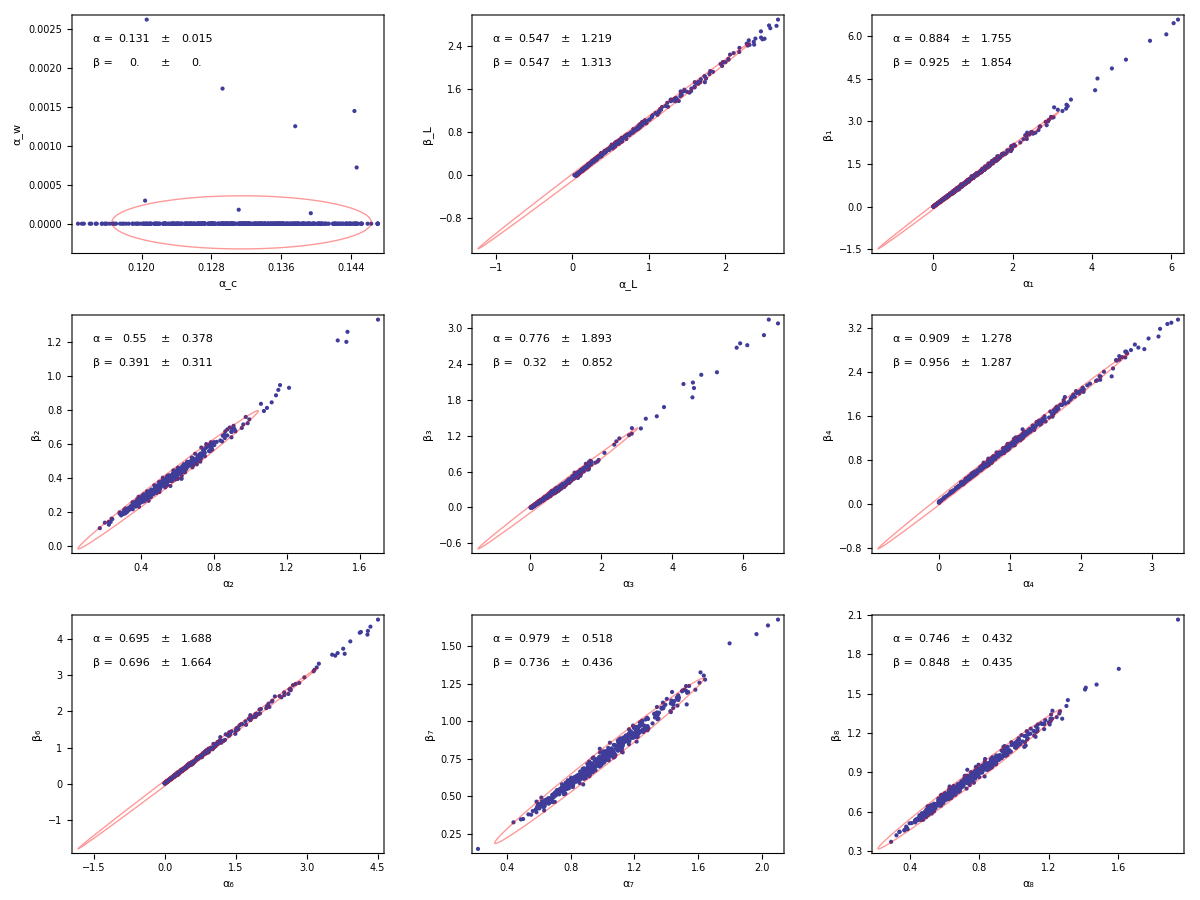

```mathematica
save=Grid[Listplots[[1]]~Partition~3]
```

```mathematica
Export["lduncert.pdf",save]
```

lduncert.pdf

```mathematica
SystemOpen[DirectoryName[AbsoluteFileName["BS27.pdf"]]]
```

```mathematica
SetDirectory["C:\\Users\Alex\Desktop\Grad School Shit\PHYS605\Project"]
```

C:\Users\Alex\Desktop\Grad School Shit\PHYS605\Project

```mathematica
Pe2 = Import["data2.csv","Table"]
```

{{{0.12086251918822824,,2.009795118749411,,31.418758285956436,,-0.45252271994203375,,-4.012037322888835,,-0.8477627806790102,,-28.975314384186504,,1.7017822704432657,,-0.7732903819605532,,10.21239629495383,,-3.4394211668402922*^-9,,2.1516987974928834,,32.47483391866867,,«9975»,-21.747140897410514,,3.7647281767426803,,-0.000175608484109351,,-1.7018738830787463,,3.5865422712367887,,0.5634767813750798,,0.04825550332651782,,6.943330232170831,,1.3967934982450863,,-3.516092794171279,,-17.937426833895564,,3.91610699465078}},«3»,{«1»}}

```mathematica
actual ={ 0.125120447,0.2453021,0.7491892366497901,0.44118386223923545,0.17193008586682357,0.922720059201386,0.7124062074680186,0.5898966317547063, 0.8498145306514904, 0.7778254794939592,0.007256062876177221,0.240343, 0.7902230762443223,0.31166228728883012,0.06655575840953443,0.9795814487355847,0.6580558294204786,0.599771396211936,0.6398638788598377,0.8907779882884594};
```

```mathematica
usefulldata = Flatten[Table[StringTrim[Pe2[[3,i]],("{"|"}"|",")],{i,1,Length@Pe2[[3]]}]];
usefulldata = ToExpression/@usefulldata;
usefulldata= usefulldata~Partition~20;
```

```mathematica
Pe3 = Import["approxsys.csv"];
```

```mathematica
stuff = Abs@Transpose@usefulldata
x2 =Table[{},{i,1,1}];
y2=Table[{},{i,1,1}];
Do[
xstuff = stuff[[j]];
ystuff = stuff[[j+10]];
rem = Filter[xstuff]∪Filter[ystuff];
AppendTo[x2[[i]],Delete[xstuff,rem]];
AppendTo[y2[[i]],Delete[ystuff,rem]],
{j,1,10},{i,1,1}]
```

{{0.133792,0.110622,0.117008,0.120491,0.137632,0.117243,0.130048,0.122286,0.12619,0.126505,0.123581,0.120064,0.116627,0.137072,«473»,0.12126,0.121725,0.113143,0.12714,0.124412,0.121939,0.122557,0.125239,0.129375,0.125839,0.114228,0.105703,0.133673},«18»,{«1»}}

```mathematica
Grid[Table[
Show@@
Flatten[{
Table[{ListPlot[{{Mean[x[[i,j]]],Mean[y[[i,j]]]}},PlotStyle-> col[[i]],PlotStyle-> AbsolutePointSize[Large]],
Graphics[{Thick,col[[i]],Opacity[.9],EllipsoidQuantile[Transpose@{x[[i,j]],y[[i,j]]},.95] }]},
{i,1,3}],{
ImageSize-> 400,Frame-> True,PlotRange->All,FrameLabel ->{Style[axes[[j]],FontSize->18],Style[axes[[j+9]],FontSize->18]},
Axes-> False,FrameTicksStyle->Directive[FontSize->17]}}],{j,1,9}]~Partition~3];
```

```mathematica
means =Flatten[{ Table[Round[Mean[x2[[1,i]]],10.^-3],{i,1,10}],Table[Round[Mean[y2[[1,i]]],10.^-3],{i,1,10}]}]
sddev = Flatten[{ Table[Round[2*StandardDeviation[x2[[1,i]]],10.^-3],{i,1,10}],Table[2*Round[StandardDeviation[y2[[1,i]]],10.^-3],{i,1,10}]}]
othermeans = Flatten[{ Table[Round[Mean[x[[1,i]]],10.^-3],{i,1,9}],Table[Round[Mean[y[[1,i]]],10.^-3],{i,1,9}]}]
otherstd = Flatten[{ Table[Round[2*StandardDeviation[x[[1,i]]],10.^-3],{i,1,9}],Table[Round[2*StandardDeviation[y[[1,i]]],10.^-3],{i,1,9}]}]
```

{0.013,0.345,2.026,0.335,3.005,1.464,0.433,2.086,0.526,0.441,0.024,0.396,2.124,0.27,1.438,1.478,0.442,2.04,0.442,0.446}

{0.131,0.547,0.884,0.55,0.776,0.909,0.695,0.979,0.746,0.,0.547,0.925,0.391,0.32,0.956,0.696,0.736,0.848}

{0.015,1.219,1.755,0.378,1.893,1.278,1.688,0.518,0.432,0.,1.313,1.854,0.311,0.852,1.287,1.664,0.436,0.435}

```mathematica
otherstd=Insert[otherstd,"N/A ",7];
otherstd=Insert[otherstd,"N/A ",17];
```

```mathematica
othermeans
```

{0.131,0.547,0.884,0.55,0.776,0.909,0.695,0.979,0.746,0.,0.547,0.925,0.391,0.32,0.956,0.696,0.736,0.848}

```mathematica
Table[{ScientificForm@Mean[Table[x[[1,j,i]]-y[[1,j,i]],{i,1,Length@x[[1,j]]}]],
ScientificForm[2*StandardDeviation[Table[x[[1,j,i]]-y[[1,j,i]],{i,1,Length@x[[1,j]]}]]]},{j,2,9}]//TableForm
```

```mathematica
Table[ScientificForm[actual[[i]]-actual[[i+10]]],{i,2,10}]//TableForm
```

```mathematica
stuff = Abs@Transpose@ParamEstimates[[3]]
x =Table[{},{i,1,1}];
y=Table[{},{i,1,1}];
Do[
xstuff = stuff[[j]];
ystuff = stuff[[j+9]];
rem = Filter[xstuff]∪Filter[ystuff];
AppendTo[x[[i]],Delete[xstuff,rem]];
AppendTo[y[[i]],Delete[ystuff,rem]];,
{j,1,9},{i,1,1}];
```

{{0.133661,0.145065,0.144738,0.121968,0.132606,0.127454,0.124841,0.139499,0.136536,0.125735,0.137253,0.133537,0.134491,0.124264,0.136813,0.143584,0.128998,0.142417,0.127346,0.132935,0.121969,0.130268,0.133152,0.139022,0.129356,0.138133,0.145071,0.130292,0.138487,0.14803,0.14667,0.128443,0.137383,0.130481,0.122355,0.118786,0.135615,0.124835,0.126391,0.145853,0.138627,0.131002,0.148392,0.144066,0.134271,0.118502,0.132521,0.127638,0.139567,0.121915,0.124984,0.141072,0.134249,0.129982,0.129979,0.12563,0.143591,0.12315,0.126504,0.130278,0.144267,0.127316,0.135785,0.131737,0.135205,0.136549,0.130824,0.138926,0.149166,0.128843,0.127177,0.133833,0.135363,0.13309,0.129959,0.122001,0.119833,0.151787,0.134728,0.122747,0.135743,0.132835,0.129072,0.146022,0.142198,0.126321,0.127219,0.129029,0.126664,0.143669,0.129045,0.123934,0.13637,0.138815,0.140876,0.131747,0.132108,0.142254,0.111672,0.139757,0.141359,0.139491,0.143347,0.124764,0.132917,0.146999,0.119961,0.124741,0.128785,0.141345,0.13413,0.123722,0.135926,0.132248,0.126439,0.134886,0.119763,0.12603,0.126835,0.141768,0.151365,0.128613,0.127756,0.127062,0.122985,0.129814,0.145125,0.140506,0.132898,0.128556,0.131861,0.137329,0.143964,0.125223,0.132641,0.128332,0.125866,0.137397,0.134989,0.131507,0.133337,0.145756,0.147073,0.1393,0.126046,0.128862,0.135214,0.125851,0.143915,0.122407,0.135828,0.129407,0.136711,0.138623,0.151346,0.14163,0.130193,0.13638,0.130243,0.13772,0.128973,0.132801,0.134108,0.125342,0.129565,0.136131,0.139462,0.136365,0.115903,0.125327,0.142377,0.132203,0.135042,0.127147,0.133295,0.138637,0.138,0.141281,0.133218,0.13221,0.134698,0.135685,0.143378,0.12822,0.141545,0.123443,0.142865,0.125026,0.129344,0.132078,0.139495,0.137419,0.123555,0.13251,0.111614,0.133927,0.12821,0.145557,0.13478,0.143326,0.129489,0.136989,0.136802,0.16163,0.138218,0.135177,0.131961,0.126969,0.115014,0.128665,0.136698,0.136542,0.141037,0.126776,0.141036,0.130318,0.116429,0.130404,0.12136,0.139466,0.132662,0.127682,0.132307,0.138546,0.138338,0.144756,0.134079,0.130042,0.129441,0.124317,0.138428,0.121812,0.136333,0.145572,0.131845,0.133957,0.145516,0.142861,0.144514,0.128915,0.133775,0.125558,0.123825,0.138056,0.12553,0.129778,0.143684,0.139504,0.141448,0.128384,0.136901,0.129818,0.123544,0.132732,0.13533,0.123188,0.143761,0.131129,0.140073,0.137348,0.144567,0.141001,0.1375,0.130357,0.136468,0.127957,0.125194,0.129062,0.143612,0.111749,0.144086,0.136784,0.117822,0.137101,0.134425,0.138143,0.119966,0.128222,0.123347,0.145849,0.133915,0.137636,0.134706,0.133376,0.134067,0.133443,0.134574,0.120143,0.131506,0.136835,0.120153,0.14954,0.139722,0.131769,0.138166,0.133754,0.139062,0.126564,0.126447,0.133455,0.124574,0.13681,0.14821,0.135676,0.14075,0.147122,0.132463,0.133475,0.119265,0.136699,0.130503,0.127263,0.143191,0.130548,0.132097,0.135477,0.139719,0.125563,0.125418,0.143887,0.134292,0.134289,0.135501,0.142946,0.138927,0.126867,0.127409,0.129713,0.140461,0.137122,0.124868,0.128214,0.134323,0.129366,0.131515,0.130695,0.135457,0.147812,0.126248,0.134028,0.121971,0.136063,0.131083,0.133799,0.138207,0.13912,0.118415,0.123685,0.141293,0.125543,0.13575,0.132208,0.136618,0.120371,0.147482,0.130518,0.135944,0.124354,0.121638,0.122402,0.13696,0.136015,0.139299,0.122478,0.124993,0.117743,0.142063,0.126226,0.120637,0.132352,0.129459,0.138809,0.12171,0.114564,0.118651,0.141322,0.132891,0.132924,0.119819,0.127973,0.130609,0.143706,0.118721,0.129802,0.127695,0.132447,0.135102,0.131134,0.144229,0.127505,0.135772,0.124968,0.127063,0.122261,0.132927,0.121459,0.132436,0.134403,0.122029,0.145758,0.128048,0.142626,0.143288,0.137716,0.136719,0.132773,0.135244,0.122531,0.121656,0.133643,0.139725,0.143333,0.131454,0.127486,0.12637,0.14004,0.142182,0.125427,0.141201,0.138002,0.13121,0.142624,0.134018,0.121949,0.121153,0.125736,0.13998,0.12836,0.138335,0.134912,0.130047,0.148736,0.134716,0.12751,0.144993,0.128255,0.125759,0.140595,0.135696,0.136794,0.113206,0.1288,0.135756,0.134965,0.136383,0.124176,0.129875,0.138369,0.140965,0.131195,0.125783,0.134638,0.127108,0.136263,0.127654,0.133,0.147227,0.119249,0.128609,0.137501,0.13069,0.134493,0.120988,0.138923,0.136791,0.134467,0.13035,0.124328,0.148818,0.134739,0.121123,0.128746,0.141503,0.133293,0.127973,0.131378,0.11908,0.130992,0.132935,0.131608,0.123722,0.130084,0.139005,0.137966,0.134969,0.135022,0.143592,0.127504,0.122333,0.132979,0.149877,0.140531,0.127348,0.129132,0.133808,0.140305,0.135348,0.13887,0.139173,0.141493},{0.813136,0.888739,0.0845091,0.0479425,0.211423,0.0567395,1.2425,0.0778154,0.266566,0.503947,0.448312,0.591946,0.650957,0.0474587,0.257954,0.212043,0.154798,0.0890629,0.305332,0.402611,0.277326,0.791791,0.743941,0.390558,0.796541,0.066385,0.167745,0.175866,0.439385,0.231938,0.0751463,14.6725,1.01935,0.583274,0.251047,0.0478436,0.59437,0.11747,0.600506,0.0770404,10.9839,0.163938,0.817172,0.516276,0.0725127,0.321861,0.287657,1.26015,1.48497,0.68912,0.683191,0.083975,0.450437,0.103405,0.122798,0.445796,1.4364,0.428603,1.36217,0.137035,2.03219,0.131948,0.0994518,0.27307,0.209808,0.120589,0.305194,0.0757806,0.288271,0.108408,0.22727,0.431294,0.065506,0.388727,0.192484,0.840814,1.22815,0.163208,0.705602,0.313148,1.05322,0.843686,0.613929,1.20913,1.20141,0.279199,1.0763,4.88985,0.223581,0.0713851,0.358444,0.184487,0.0522044,0.34896,0.157187,1.26601,0.367951,0.0683045,1.26607,4.60155,0.172062,0.267615,0.874973,0.0616039,0.752111,1.31638,1.45319,1.42155,0.393357,0.68542,1.39393,6.77219,0.656865,1.02528,0.690593,1.44752,0.644972,3.00515,0.81796,6.69107,0.54916,0.0708613,0.712651,0.103048,0.0948114,0.630676,0.324214,0.336331,0.543625,0.444581,0.334545,1.05892,0.970538,1.38841,0.268124,1.03002,0.63808,0.158665,0.698778,0.0677646,0.0597217,0.720353,0.430738,1.60478,0.842888,0.571468,0.730029,0.307435,0.792431,0.349686,0.126356,0.217854,0.0646488,0.813888,0.113735,0.0536094,0.518673,0.0843056,4.35716,0.725065,0.733747,0.392193,2.41304,0.953246,1.31171,1.07317,0.118832,0.335515,0.474798,0.404138,0.0934693,2.66691,0.136486,0.545839,0.163596,0.285089,0.153044,0.0692199,1.63938,0.431741,0.120736,1.47243,0.0703994,0.0457344,0.0902422,0.942278,0.103851,0.845655,0.967903,0.166144,0.336822,1.05366,0.0691573,0.0574392,0.980075,1.84869,0.330362,1.08758,0.137273,0.0803812,0.784465,0.685065,0.501098,0.0701248,0.350034,0.0531282,0.328939,1.4282,0.330764,0.314849,0.384993,0.510474,0.0726543,0.182394,1.36547,0.569111,0.181936,0.314613,0.264232,0.933775,0.741468,0.447677,0.0607975,0.0524436,0.315701,2.155,0.782453,0.929165,2.5576,0.668598,0.991738,0.922397,0.0598658,0.287103,0.540614,1.02594,0.0786334,0.421252,0.0754435,1.00383,1.32049,0.211851,1.10171,1.27593,0.208644,0.218854,0.0578511,1.86671,0.0943258,0.549067,0.0672068,1.63687,0.601325,0.763788,0.213268,0.217768,0.0712112,0.17522,0.163762,0.384175,0.0583371,0.29689,0.762784,0.329295,0.813251,0.351813,1.80951,7.74972,0.0994021,0.441053,0.817558,0.0763481,1.29418,0.261956,0.291392,0.0920536,0.310594,0.716868,0.257495,0.0696299,0.758682,0.0550344,0.319141,3.22481,0.704853,0.614257,0.289142,0.504236,0.655297,0.0609609,1.68908,0.0758123,0.515289,0.339056,1.23287,0.362085,1.0664,2.73609,0.170141,0.0807553,0.056596,0.430546,1.23144,0.0757787,0.179079,0.0632403,0.222222,0.121301,2.96992,0.909489,0.060203,2.8505,0.465789,1.13429,0.641952,0.0685672,0.191268,1.70401,0.706192,1.10427,0.75648,0.0576488,0.632575,0.0738164,0.201183,0.714183,0.817734,1.49202,0.111799,0.193832,0.507705,0.593872,0.192258,0.337181,0.792321,0.357474,0.338344,0.477239,0.0631332,0.173912,1.57092,1.4544,0.11938,0.164053,1.25405,0.06603,0.174604,0.261912,0.717368,1.17807,0.410753,0.479629,2.62143,0.0597701,0.401218,1.17745,0.162187,0.628767,0.409124,0.132093,0.839738,0.150698,1.34816,0.224119,2.99441,1.22047,0.284238,0.154933,1.00755,0.205036,0.365107,0.426592,1.51029,1.10592,0.591915,0.201791,0.0551619,1.49409,1.5091,0.49681,0.253897,0.120439,1.40702,0.634357,0.263677,0.745359,1.31379,1.29369,0.249444,0.625979,0.410682,0.593601,0.170469,0.261255,1.84333,0.368417,0.274325,0.699253,0.158238,0.434966,0.741261,0.520006,0.0583768,0.160073,0.244205,0.389146,2.12475,0.145398,2.13636,1.7154,0.161175,1.04734,0.117375,3.0295,0.0516763,0.752527,0.770305,0.416029,0.110393,4.7931,0.351675,0.192694,0.311756,0.428214,1.03637,0.300766,0.216534,0.33781,1.58939,0.271086,2.82161,0.0567803,0.635664,0.324521,0.217349,0.733262,0.0713946,0.0674221,0.627629,0.0696934,0.626972,0.915988,0.058373,0.611595,0.14397,1.04886,0.217793,0.799385,0.35763,0.777172,7.24712,0.115662,0.159368,0.156556,2.53753,0.628302,0.122003,0.821813,0.285356,0.0723449,0.307636,0.121864,0.0526331,0.0837609,1.78375,2.38747,0.150415,0.937383,0.134378,0.0834393,0.702298,0.708061,0.0994916,0.255556,0.221067,0.0978164,0.0462047,0.210827,0.0822593,0.0597301,1.65444,1.69178,0.108498,0.0883422,0.236999,0.136515,0.12408,0.182631,1.0972,0.148351,1.88178,0.0811955,1.02863,1.2543,1.23666,0.0815894,0.483433,0.798351,0.518398,0.319681},{0.887011,0.464099,0.482958,0.498675,0.708617,1.00459,1.18328,0.114781,0.00632651,0.374005,1.06229,0.983132,0.02934,0.695211,0.466582,1.27803,0.98293,0.531791,1.54961,1.17194,1.56047,2.11412,0.27842,0.746624,0.643648,0.497316,0.0729192,0.0551367,2.52256,0.0073257,0.0466717,0.581553,0.851975,2.25265,1.02466,0.00114443,0.344396,0.00642457,0.96447,0.385923,0.430996,0.846833,0.0387421,0.417853,1.5259,0.846305,0.49374,0.153364,0.791376,0.719093,0.495528,0.167207,0.25685,2.22197,1.58649,0.0469685,0.873224,0.572446,0.189106,0.00371487,0.915195,0.118531,0.739022,0.127313,0.0720548,0.572731,1.0979,0.965046,0.643791,0.78151,0.568298,1.59182,1.79968,0.516431,0.364678,0.48335,1.54113,0.000392614,1.08532,1.31086,0.399415,0.186402,1.71492,1.1967,0.544722,0.958833,3.32373,0.271839,0.498382,5.60442,0.188625,0.494279,1.36723,0.957427,0.523207,0.692481,1.49289,0.521698,0.731068,0.392835,2.53439,3.4083,0.769895,0.50865,0.0970872,1.62304,0.16377,0.960418,1.90415,0.526684,0.279168,1.51174,0.89571,1.17874,1.67396,1.2949,0.111055,0.841305,0.846563,3.89896,0.128576,0.979736,0.531048,0.00643724,0.0287194,3.39576,0.291554,1.30079,0.325134,0.653473,0.906476,0.594959,1.30485,0.413461,1.29891,0.850992,0.505446,0.846351,0.442262,0.513682,2.51131,0.740703,0.804466,0.338975,1.51639,1.32399,1.30654,0.583426,0.244303,0.982819,0.244295,0.507505,0.935154,3.04206,0.00380142,1.0144,1.82666,1.28847,1.33628,0.506728,1.24597,1.73252,1.2008,0.573368,0.121146,0.307365,0.527139,0.673422,0.0122475,1.23477,2.32995,0.488313,0.918664,0.826684,0.755666,0.921939,0.486159,0.81566,1.27283,0.400814,0.530872,0.390774,0.548985,1.05184,0.00926569,0.573881,0.509939,0.574558,1.3386,1.94079,0.313513,0.00457628,0.18695,2.19151,0.867742,0.250558,0.561128,0.240828,0.738275,0.0109742,0.266283,0.870442,0.677412,0.852362,0.839516,1.00237,0.200972,1.60102,0.672901,0.52108,1.04777,1.32447,1.20248,0.302498,0.226814,0.043257,1.90674,0.696684,1.16392,1.4196,0.947219,1.22795,6.81392,0.912591,2.40526,0.754659,0.473754,0.372771,0.503847,0.412051,0.347756,0.649268,1.00026,0.633021,1.72628,1.20304,0.939618,0.399889,0.647682,0.735966,0.801718,0.978411,2.20841,0.219651,0.552467,0.22165,0.761104,0.429597,0.502321,0.570174,0.601166,0.627388,0.373864,0.275947,0.193559,0.722087,0.885368,0.889485,0.509029,1.66796,0.497228,1.28425,1.50424,0.148782,0.149595,5.3239,2.07009,0.482519,0.253499,0.339375,0.528929,1.5693,0.499422,0.666654,0.633734,0.416945,2.48416,0.0855511,0.417965,0.504737,0.587054,1.51298,0.537165,0.769805,0.914952,1.1026,0.634497,0.628889,0.594735,0.843875,0.63014,0.00469468,0.540012,1.6745,2.2256,1.0993,0.724251,0.227104,0.498872,1.04561,1.94267,0.689555,3.91079,0.572604,0.00447896,0.885311,0.419555,0.731796,1.04776,1.22739,0.934968,0.311365,0.553739,0.921838,1.07739,0.899326,5.30632,0.16485,0.496939,0.862006,1.33977,0.564417,2.53759,1.309,0.491509,2.29435,1.4171,0.516003,4.42221,0.505576,1.14496,1.07188,2.9433,0.256308,1.85727,0.315636,0.70323,1.4648,0.797294,0.520765,0.237913,0.746557,0.664081,0.826276,1.15141,0.522491,1.48944,1.47257,0.297097,4.97531,1.20747,0.293492,0.738287,0.705681,0.74984,0.828428,0.90724,0.845548,1.33033,0.611226,0.63784,0.00356761,6.66246,0.491083,1.0972,0.12989,0.739998,0.910609,0.650643,0.490081,0.100256,0.0376791,0.603783,1.94966,0.198195,1.34749,0.488743,0.265324,0.699927,0.563661,0.343705,0.502519,0.333591,2.31576,1.02871,0.00368968,0.388733,0.504322,0.795582,0.311704,0.251667,0.16364,1.19257,0.49199,0.579756,1.76688,0.106435,0.888716,1.12011,1.17404,1.17116,1.49301,0.694343,0.49582,1.9604,0.82546,0.717164,0.395219,0.414714,0.317109,0.994049,0.763778,0.288119,0.350894,2.99419,0.358442,2.86987,1.30918,0.498248,0.491534,0.527766,2.60771,0.860871,1.2306,1.31606,0.378614,1.1845,2.8218,0.54425,0.224492,1.60395,0.0179929,0.115029,0.91739,0.953287,2.06292,0.683894,1.77514,0.703992,1.02277,0.410631,0.154261,1.57425,1.33554,2.4972,1.13137,0.21242,0.412172,0.33468,0.435745,1.47252,0.501072,0.670521,2.22406,3.22281,0.477629,0.276822,0.0533347,0.503024,1.31279,0.520348,1.20281,0.00470164,1.12334,0.952501,0.471659,2.56714,1.03597,0.209346,0.844254,0.263486,3.77548,0.960025,0.423551,0.0682458,0.529746,0.62291,1.42754,1.65794,1.05461,0.520042,0.710339,0.0436114,0.651065,1.64413,1.22958,0.483084,0.259056,0.310315,0.653169,0.987803,0.166227,1.56055,1.54556,0.252161,0.629036,0.834402,0.730831,0.769089,1.13223},{0.554523,0.516211,0.712155,0.499912,0.485969,0.620791,0.407642,0.831347,0.744436,0.586036,0.460243,0.400337,0.803758,0.62131,0.464554,0.535868,0.45652,0.446868,0.606917,0.433033,0.546686,0.512951,0.51996,0.442342,0.518597,0.896449,0.477444,0.758569,0.572171,1.04777,0.621036,0.385339,0.433432,0.649908,0.514357,0.917712,0.502792,0.660445,0.548487,0.850739,0.536137,0.467342,0.475299,0.634395,0.416259,0.520113,0.962641,0.44021,0.488977,0.453286,1.16656,0.613635,0.585865,0.531135,0.556492,0.537819,0.458121,0.430332,0.510895,0.709264,0.4613,0.976331,0.453009,0.730856,0.477496,0.506934,0.501432,0.568234,0.494564,0.476372,0.808886,2.02938,0.446517,0.617544,0.561107,0.435691,0.433186,0.694334,0.474342,0.520819,0.437225,0.563239,0.426661,0.365512,0.555057,0.546206,0.396938,0.598292,0.766554,0.718147,0.422197,0.634451,0.383607,0.431474,0.510562,0.453624,0.382976,0.416646,0.415382,0.440235,0.61811,0.759912,0.458443,0.441606,0.647547,0.461675,0.46694,0.415707,0.570959,0.688165,0.41632,0.407534,0.399782,0.550923,0.641295,0.606477,0.431354,0.536787,0.372106,0.433602,0.394988,0.312642,0.775409,0.673244,0.564212,0.43102,0.311183,0.704878,0.581295,0.460311,0.358408,0.430237,0.422278,0.446314,0.56542,0.369918,0.531077,0.441968,0.589382,0.827313,0.76038,0.352165,0.418765,0.393133,0.918986,0.470883,0.486883,0.344242,0.419492,0.384277,0.417098,0.532056,0.594868,0.456218,0.723944,0.660055,0.449968,0.323155,0.587251,0.542621,0.424858,0.38183,0.403263,0.413304,0.491478,0.560657,0.446288,0.396525,0.53689,0.593531,0.328244,0.365158,0.650943,0.576898,0.734624,0.395677,1.23028,0.553304,0.264634,0.326358,0.833944,0.40555,0.550927,0.588347,0.569023,0.365014,0.340576,0.471023,0.619377,0.464452,0.680488,0.81464,0.659993,0.562897,0.558646,0.467847,0.568731,0.419724,0.322421,0.267508,0.486469,0.607895,0.477021,0.339184,0.55044,0.494012,0.514043,0.466474,0.385713,0.411521,0.357444,0.464164,0.358357,0.362594,0.623059,0.454348,0.50505,0.710648,0.453878,0.28495,0.441218,0.510202,0.573343,0.581996,0.631621,0.444123,0.535414,0.365534,0.4757,0.521687,0.359397,0.51326,0.550024,0.49101,0.554727,0.614022,0.578145,0.60666,0.526464,0.510645,0.356836,0.348275,0.485196,0.61714,0.526842,0.459785,0.550989,0.430804,0.702494,0.529684,0.46412,0.392308,0.368346,0.323336,0.904296,0.666248,0.510402,0.509261,0.828588,0.545585,0.824414,0.509818,0.490549,0.728064,0.377199,0.500175,0.351352,0.95685,0.355352,0.764173,0.848605,0.577854,0.371756,0.423281,0.625522,0.661979,0.579666,0.492575,0.63404,0.76881,0.446533,0.539081,0.44677,0.40105,0.567159,0.499298,0.394608,0.722458,0.40742,0.764101,0.346034,0.653071,0.765919,0.637645,0.422524,0.567878,0.534279,0.449824,0.467148,0.373826,0.684471,0.419056,0.441423,0.80855,0.787615,0.557981,0.320294,0.666227,0.509783,0.463727,0.742228,0.379409,0.458785,0.530619,0.379478,0.0656071,0.92834,0.736311,0.397214,0.449855,0.378579,0.334345,0.60159,0.400903,0.64716,0.693582,0.555972,0.364273,0.553731,0.46936,0.50466,0.558971,0.584589,0.703546,0.654054,0.583145,0.457769,0.397118,0.653401,0.692525,0.468967,0.643635,0.534669,0.708262,0.456364,0.683934,0.468372,0.625687,0.479439,0.458808,0.584395,0.469857,0.277885,0.791181,0.585851,0.38426,0.51014,0.438119,0.375801,0.518547,0.450383,0.966781,0.579418,0.852591,0.470134,0.454163,0.349241,0.532329,0.593817,0.57672,0.469876,0.380384,0.573891,0.524132,0.631666,0.528971,0.744343,0.41305,0.374958,0.697184,0.736098,0.487246,0.487869,0.619221,0.522238,0.429776,0.421615,0.507358,0.59052,0.498947,0.677576,0.401625,0.513547,0.502191,0.550657,0.642332,0.555687,0.402742,0.504994,0.422853,0.645995,0.392021,0.387371,1.09612,0.456365,0.627855,0.500312,0.625493,0.42071,0.406766,0.437608,0.484936,0.534286,0.432615,0.682709,0.473781,0.390279,0.41312,0.655837,0.51655,0.463184,0.339246,0.446461,0.469975,0.639209,0.498466,0.461774,0.589652,0.740546,0.432755,0.545568,0.900964,0.447352,0.468894,0.53243,0.408414,0.55685,0.39093,0.592665,0.464118,0.308864,0.610253,0.540228,0.579962,0.579252,0.467552,0.772168,0.460335,0.08144,0.524665,0.512115,0.690104,0.727994,0.433601,0.462646,0.96347,0.521067,0.390754,0.666791,0.493137,0.524014,0.671171,0.460869,0.452312,0.403418,0.300746,0.587125,0.783153,0.436106,0.46436,0.447892,0.571054,0.46211,0.476697,0.456397,0.46376,0.531692,0.372835,0.44798,0.40212,0.454436,0.336689,0.456329,0.510287,0.45341,0.325617,0.585552,0.43675,0.464868,0.39427,0.357463,0.471744,0.589666,0.580576,0.365695,0.497064,0.365067,0.489061,0.462975,0.571487},{0.219071,0.341286,0.712206,0.724292,1.98692,1.73003,0.468423,2.23285,0.735335,1.74231,1.21892,0.670383,0.384332,0.757541,1.05125,1.07573,13.8076,1.93764,0.0578928,1.07051,1.33914,0.266512,0.0869556,0.0742783,6.11383,0.512328,0.544342,0.597907,1.52382,0.483515,1.94293,0.956549,0.801527,1.2364,0.270016,0.0761303,4.41712,1.1426,0.0435939,0.366485,1.68158,0.0533367,0.152238,3.31735,0.714077,0.741878,0.70588,0.380547,8.06938,0.575809,0.47263,0.58003,0.864055,0.106755,0.451545,0.620473,1.66491,0.168493,0.436606,0.631513,3.78004,0.957167,0.408394,0.711373,0.719406,0.871031,0.485117,0.818439,2.56946,0.489589,0.639187,2.4582,0.205935,0.972262,1.45619,0.739833,0.702995,0.196494,0.734172,0.230855,1.61052,0.392759,0.652152,0.960738,0.324445,0.621043,1.60473,1.13139,0.704899,1.21137,0.787905,0.683191,0.526372,0.960221,0.799078,0.652405,0.593542,0.206875,0.493006,0.415752,1.69595,1.46087,0.632252,1.44868,0.952537,1.68898,0.154024,1.13328,0.389864,0.864951,0.164593,3.87387,0.888719,2.83129,0.227324,0.271935,0.655964,0.792785,1.7538,0.693112,0.407072,0.35196,1.02292,0.636642,0.593311,0.52042,0.646043,0.378754,0.372515,0.0765934,0.994865,1.06848,0.122548,0.334448,0.626065,1.131,2.84482,0.409621,0.130704,0.636064,0.137007,0.592637,1.52858,0.30024,0.245759,0.85218,0.071406,0.252424,0.767774,3.81083,0.990214,0.0574082,0.207256,0.428533,0.273663,0.201944,0.198231,12.1527,4.43829,0.264014,5.84076,0.244987,0.20927,0.789005,0.91431,0.230692,0.745124,0.196603,0.84536,0.293886,0.318662,0.123363,31.7485,0.723045,0.400552,0.828797,0.67561,0.495464,9.48675,0.495515,0.0651963,0.397337,0.277551,0.848477,0.788878,1.40303,0.0143595,1.30768,0.391586,62.9924,0.322655,0.783947,1.02727,0.122045,0.549448,0.239067,1.18056,0.334534,0.809879,18.6184,5.98169,0.363633,1.77615,0.695727,3.6112,0.557519,0.617371,0.343917,0.125469,0.398875,0.415002,0.372294,0.498138,0.803489,0.967075,0.68292,0.808058,0.749475,5.24878,0.375184,0.213825,1.36558,0.468173,0.0347356,0.895125,0.214802,1.25303,0.525198,4.12529,0.442882,0.852319,1.07979,0.153346,0.498897,0.844038,0.584682,0.770137,0.447319,0.730381,0.765735,0.836504,0.331269,0.962028,0.904319,0.0417448,0.521454,1.0533,1.69234,0.61513,1.55143,0.239431,0.525245,0.555769,1.80255,13.4661,0.389458,0.863614,0.157979,0.0299415,2.4664,0.557568,0.262053,0.246094,0.186574,0.739401,0.203263,0.198739,4.32002,0.221461,0.587928,0.879798,0.205156,0.132674,1.46785,0.919175,1.36907,12.4939,1.05601,0.246537,0.406043,0.636762,0.213626,0.54095,0.130492,0.0562086,0.921187,0.698398,0.276817,8.5358,0.569488,1.05021,0.715222,8.99514,0.111481,0.359975,3.39968,0.400082,1.04115,0.253078,0.194106,0.71492,0.598692,2.35829,0.737699,0.72743,0.154574,1.61295,0.416296,0.364748,0.670628,1.5395,9.79811,0.704162,0.0603238,0.424008,0.810566,0.880064,0.951251,0.19679,0.26472,0.449744,0.329108,0.329554,0.527612,0.71535,0.0399128,0.373781,0.813844,0.579648,0.509744,0.41192,1.30308,12.893,1.34148,0.978144,0.297088,0.777344,0.865123,0.0385216,0.720336,0.716936,17.8735,0.463894,0.0629536,0.548721,0.668069,0.261462,0.0335287,0.332255,0.0782183,0.879722,0.581697,0.727768,1.14718,0.801211,0.571922,0.0981103,0.209996,2.82424,0.782432,0.412438,1.02969,2.69928,0.70028,1.05968,0.0874128,2.4732,0.0727079,0.170681,0.828156,0.164854,0.626682,0.266193,0.2944,1.55477,0.190852,0.240202,6.51741,0.845491,0.178514,0.608933,0.765536,2.87354,0.160813,0.589893,1.01826,0.432338,1.03779,0.873446,1.90069,0.0418284,1.13178,0.982891,0.652973,0.16597,20.6704,0.35908,0.304451,0.283368,0.434918,0.320773,0.579442,0.180315,0.371261,0.230248,0.71303,2.23667,19.8113,0.236437,0.212234,0.348829,3.3007,0.607495,1.80716,1.96706,0.0610863,0.949446,0.622771,0.0544922,0.231151,0.524598,1.78585,1.2396,0.180178,0.0720656,0.355875,0.125843,0.441555,0.842661,1.09259,0.795288,0.755751,1.35406,0.612977,13.3296,0.712797,0.0424664,0.595913,0.159369,1.13692,0.201095,0.682538,0.436063,0.488035,0.549346,0.405414,0.723448,0.432193,0.345631,0.3636,0.168021,0.74935,0.863846,17.0862,0.771053,1.1228,0.727439,0.138042,1.2144,0.919545,1.50666,0.534503,0.585648,0.0695555,11.91,0.17583,20.6638,1.10228,0.307485,0.0998232,0.203323,1.59971,0.917908,0.6522,0.612683,0.868739,0.459171,0.671086,1.10536,0.418177,1.03651,0.905473,0.921091,0.789978,3.43993,38.1917,1.10496,0.409555,0.131264,4.33962,0.848457,0.995458,1.14666,2.04629,0.378973,0.975188,0.324639,0.5835,0.638322,0.119838},{1.37434,2.41612,0.377857,0.499032,0.326997,0.84473,0.972889,0.179976,0.441963,1.16359,1.18818,0.358626,0.91344,1.17324,0.595997,0.392604,0.831013,0.734849,0.771218,0.881797,0.629141,1.27162,0.63467,0.91894,0.487176,0.524436,1.13129,1.07789,1.27011,0.658844,1.35518,1.58179,3.24923,1.02086,0.344941,0.482153,1.89161,0.444937,0.282602,0.66982,2.64511,0.49241,1.31515,0.626717,0.825689,0.986669,0.591799,1.3863,0.619323,3.40774,0.470528,0.449049,1.56116,0.792213,0.48411,0.851261,4.12597,1.2363,2.61214,0.356729,2.36611,0.728092,0.643298,0.710566,0.377249,1.17892,1.03484,1.20753,0.726536,0.834258,0.520209,0.452162,0.857292,0.550431,3.46996,1.01204,1.87682,0.39354,0.501539,0.199126,1.41456,2.42404,0.543431,0.742607,0.499594,1.10622,0.399926,2.01506,0.460955,0.976895,0.348449,0.307168,0.41243,0.457307,1.08035,1.61634,0.444336,0.526307,1.31668,1.61678,1.07384,1.50097,0.501974,0.403427,0.444979,1.22281,1.79413,3.00243,2.06868,0.69876,1.5823,0.997151,0.729473,1.21018,0.856071,2.03633,0.807173,5.47297,0.508811,0.774496,0.58845,0.667551,0.815503,0.470708,1.17727,0.573844,0.516103,0.701299,0.878105,0.909605,1.07812,1.59419,0.938456,1.74379,0.875499,2.33429,0.185125,0.849343,1.07084,0.399831,0.594915,6.26343,0.811983,1.38969,1.69026,0.681355,1.5539,0.54641,1.64598,0.931459,0.759225,0.492341,0.490294,0.97787,0.466232,1.42329,0.510053,0.630677,1.11231,1.89123,0.643717,0.615426,1.2528,1.63071,1.73937,1.90831,0.988639,0.698499,0.689631,0.877453,0.871905,3.08431,1.32036,0.873919,1.40092,1.25282,0.605291,0.895858,2.82856,1.10412,0.634143,0.759561,0.430709,1.77753,0.716192,4.1608,0.374506,1.8169,0.488377,1.31502,0.348014,0.839572,0.523404,1.44871,0.151835,2.20692,0.0139904,1.09107,0.408821,0.954911,2.37457,0.42643,1.33736,0.559465,0.573733,1.05744,0.577128,2.88769,0.980944,0.700717,0.272921,0.767208,0.562645,0.521743,0.854962,0.547747,1.08902,0.716256,0.858124,1.06689,0.703602,0.921671,2.09925,0.435801,0.516561,3.85666,0.493559,3.56832,4.58433,7.09408,1.57154,0.679255,0.448168,0.619362,0.516183,1.50389,0.423293,0.930521,0.568055,1.03331,1.48377,0.379162,0.252654,4.31353,0.569712,0.781718,0.385139,3.18561,0.512518,2.78376,1.07352,0.940863,1.17406,1.0438,0.434769,1.16265,1.16959,2.07874,0.569814,1.36986,0.369163,1.87305,0.450203,1.20272,1.23808,1.09245,1.98584,1.82845,0.899407,0.77123,0.546069,0.592411,1.28617,2.3482,0.638134,0.377736,0.340196,0.591738,1.73235,0.530624,0.657549,0.573277,0.586655,0.75326,0.64832,0.711093,1.0096,0.303028,0.929047,0.297708,2.12139,0.850804,1.04304,0.891848,1.18717,0.318631,1.29963,1.15794,0.422719,3.2993,1.65492,0.762757,1.64095,0.716248,0.778628,0.604947,0.397899,0.28788,1.16488,1.98565,0.477152,3.00064,0.822044,0.830534,3.62541,0.579498,0.312782,0.84136,1.39996,0.989519,1.02638,0.295529,0.483756,0.588133,0.432426,0.463962,0.707763,0.576107,0.416847,0.404391,0.64874,0.885626,0.495285,0.307765,0.528584,0.925051,0.981242,1.2749,0.662684,0.405351,0.622598,0.525172,0.868851,0.639831,1.69449,0.429937,0.59123,0.547601,2.29603,0.612533,0.567081,0.578744,0.690675,0.354675,0.280404,1.43669,3.27689,0.902181,1.09842,0.580209,1.65184,0.387351,0.267634,0.606067,3.88398,0.439401,0.723255,0.477479,1.58325,0.368052,1.12459,1.57926,3.61758,1.05469,0.50675,0.819314,0.576276,0.350865,3.45514,0.630182,0.571998,0.448419,0.838779,1.34966,0.819003,0.787834,1.93288,2.83717,0.985332,0.652347,0.63664,1.75828,0.62749,0.369304,2.40269,0.542172,1.17223,3.41771,0.366266,1.03042,1.9352,1.42062,0.69765,0.533727,0.698218,0.98803,1.46178,0.371295,2.58957,3.32594,1.2466,0.476134,0.490864,0.79278,1.63475,0.369048,0.918488,0.562558,0.377745,1.25775,1.0132,0.337031,0.55968,0.818937,1.25943,1.3393,2.48789,1.45237,1.04769,0.720983,1.0633,0.787157,1.38445,0.946787,0.837084,5.92544,0.849843,0.684897,1.35005,1.50159,0.662185,1.11681,0.702956,1.64924,0.592207,0.970664,0.603646,2.43451,0.706617,0.874519,2.51941,0.177014,0.530021,0.258263,1.6824,0.380415,0.301795,0.55087,0.400052,0.523301,0.948043,1.10012,0.971467,0.355135,2.48551,3.61399,0.692517,0.39224,4.03558,0.865534,2.17638,1.01117,0.891925,0.666543,0.884692,0.572041,0.572684,0.762382,0.465805,0.748831,0.519367,1.03628,2.40042,1.11829,0.354525,0.248442,0.34718,0.812161,6.7239,0.388191,1.53057,0.836526,1.4136,0.628871,1.34632,0.244764,0.973967,0.996449,1.00651,0.484776},{1.44129,0.73546,0.0546817,0.761695,0.410772,1.52768,3.76349,0.147417,0.237306,2.05583,0.048016,3.17055,0.00432281,0.104064,0.0845722,0.977098,0.0884342,0.270077,0.257039,0.129647,0.0342764,0.574861,2.01306,0.651215,0.322378,0.499208,0.142843,0.218631,0.841297,0.499334,0.954906,2.00733,0.925473,1.5098,1.47615,0.22144,0.558712,0.246277,0.0157472,0.140087,1.44432,0.00109164,0.518299,0.52969,0.239673,2.62891,0.0609464,1.4274,1.62602,2.22273,0.00561044,0.234777,0.310878,0.85577,1.86516,0.123816,0.438558,0.937141,0.518136,0.208704,0.0142098,0.153826,0.00424706,1.55922,0.737626,0.900532,1.44967,1.17639,0.413018,0.0011783,1.06377,0.360776,0.321976,0.806719,1.18885,0.841905,0.697802,0.568792,0.0759994,0.400797,1.34829,0.673338,0.298838,0.0561352,1.79674,0.148472,0.536451,0.98511,0.00481642,6.01835,0.771618,0.203758,0.245978,0.48718,0.188456,1.14051,0.492314,0.102719,0.100945,1.3817,2.90937,0.0772336,0.275097,0.17472,0.375236,1.76563,1.3063,0.0316633,0.47957,0.621326,0.689532,0.591485,0.13033,0.0252188,0.145218,0.883364,0.35021,1.82313,0.0744821,14.0555,0.0167195,0.433301,1.89356,0.507315,0.0307626,1.54824,0.15977,0.548633,1.05267,3.356,0.287311,0.0535107,1.35043,0.711969,0.126216,0.435556,0.064543,1.40063,0.445803,0.00180459,0.21807,0.584019,0.0423693,0.153211,0.568452,0.783993,0.490665,0.934662,4.59169,0.18924,2.12159,0.0449102,0.373044,0.0907372,0.229181,1.42871,0.447944,0.325474,1.16506,1.57186,0.533689,2.43803,0.219756,0.215184,0.162772,0.711688,0.0716533,1.16507,0.532291,0.21548,0.475505,0.16184,0.971656,0.18059,2.46811,0.906842,0.172531,0.00236187,0.438676,0.120416,3.24033×10^-7,0.434041,0.0643243,0.190285,0.110343,0.525998,0.509313,0.3175,0.615948,3.27966,0.330952,0.414231,0.0454628,0.297393,0.374343,0.726923,0.803163,0.234214,1.11506,0.983838,2.13601,0.0992776,0.731175,0.00711127,0.400634,0.165949,0.140593,0.718935,1.22195,0.485065,0.156,0.127015,0.0045454,0.377008,4.76707,0.524338,0.05049,0.245104,0.266673,0.803444,5.10791,1.06771,0.125407,0.541556,0.146878,0.0154748,0.104641,0.0709245,2.80034,1.28496,0.399471,0.477926,1.60518,0.391946,2.0411,2.83529,0.0387711,1.05803,1.51614,2.90895,0.367191,1.13133,0.197859,0.913175,0.46315,1.39256,1.08257,0.14049,0.663585,0.3995,1.21586,0.854779,0.270105,0.134765,0.1177,0.0234196,0.145474,0.723653,0.131653,0.554703,0.15183,0.33617,0.522728,0.245388,0.227987,1.59881,1.22123,1.42719,0.174613,0.562168,0.204001,0.000426317,1.06234,0.297724,0.255359,0.215591,1.18979,0.26907,1.08386,0.094752,0.159244,0.169544,0.0029232,1.08291,3.24561,0.409805,1.23868,0.0836116,0.00145335,0.506911,0.390182,0.762019,0.758651,0.188399,0.595076,0.354031,1.12929,0.0730234,0.264637,0.367386,0.00556347,0.413851,0.41844,0.244025,0.066259,0.183649,0.0144554,0.76577,0.321813,0.324999,0.344947,0.651824,0.694688,0.43516,0.971127,0.0814807,1.2958,0.00090939,0.207102,1.55424,2.34887,0.226702,1.08375,0.579482,0.137286,0.0248566,0.310147,0.538044,9.43841,0.703843,2.91297,0.272882,1.01759,0.931803,0.450254,0.459943,0.588701,0.569539,0.281419,0.502941,1.37265,2.46441,0.417894,0.249024,0.380549,1.07261,0.224027,1.4864,0.511888,2.52406,0.00192479,0.190982,0.502572,0.201033,0.835854,1.36372,1.07721,0.175239,0.946181,0.187211,0.905715,0.0179666,0.183308,0.49848,0.817026,0.682438,1.2147,0.348359,0.213265,0.178986,0.981105,0.161261,1.25628,0.860175,0.0208372,1.34003,0.460974,0.611502,0.582633,0.823122,1.75862,0.49482,0.377894,0.320941,0.196734,0.0539932,1.16853,6.66877,0.00464165,0.0818263,0.42555,5.31464,0.778577,0.00617584,0.332269,0.980045,0.0699172,1.04777,0.295391,0.0719836,1.51248,0.292178,0.224566,0.516173,0.145263,0.12381,0.19958,0.133672,0.325631,0.377596,0.102256,0.949546,1.33356,2.98104,0.149228,0.36023,2.01493,0.622448,0.00258309,1.10513,1.9931,1.58377,0.0440457,0.35917,0.873955,0.376415,1.11513,0.370935,3.73783,0.135515,0.611658,0.186105,0.738542,0.757071,0.428679,3.28718,0.210263,0.258759,5.39029,0.371572,0.165097,0.140457,0.114615,0.39634,0.0909435,2.49619,0.202678,1.00149,0.395658,0.128133,0.235092,0.392334,27.7073,0.666332,0.191855,1.42494,0.731192,0.686013,0.0373947,0.13811,0.832851,0.170135,0.340402,0.233912,1.24472,0.718033,1.40527,1.3358,1.2098,0.00914269,1.37566,0.615811,0.238435,0.0771105,0.734882,0.506076,0.373019,0.776728,1.05722,0.889198,0.295828,0.478642,1.71936,0.146204,2.27754,0.368317,0.051293,0.151731,0.358133,1.99104,1.41397,0.0721019,0.0600232,0.804178,0.419308,1.05206,0.363262,0.464127,0.670268,0.408076},{1.02168,0.844255,1.50194,1.35601,1.58921,0.776435,0.951295,1.13082,0.793965,1.71632,1.26641,1.07552,0.902869,1.73385,0.949023,0.966999,1.50079,1.39377,0.98342,0.958598,1.02925,0.933499,1.29874,0.71425,0.966127,1.13927,1.03962,1.60478,0.416173,1.35022,1.02109,0.907136,0.83594,0.923853,1.20312,1.05494,0.529381,1.32335,1.57963,1.44466,0.927862,0.865141,0.766833,0.857969,1.03023,1.15934,1.4658,0.57037,0.805389,0.699251,0.965311,0.588717,1.17371,0.958754,1.08562,0.881654,0.673518,1.09412,0.562799,0.604555,1.07338,1.48827,0.857308,0.697379,0.971329,0.809233,1.54144,0.923572,1.28559,0.964122,1.13637,1.04282,1.41351,1.25135,0.960163,0.852316,1.14135,1.0357,1.05429,0.657821,0.754768,0.788973,0.900496,0.974366,1.38664,0.816786,0.797255,0.588024,1.27889,1.14081,0.46266,0.584563,1.04879,0.994302,0.674343,0.829066,0.653965,1.08354,0.905182,1.10479,1.15729,1.28883,0.878679,0.754714,0.823764,0.732984,0.648651,0.920965,0.994417,1.19819,0.844549,0.709611,0.65419,0.765961,1.15811,0.639241,0.691883,0.588476,1.41941,14.0449,1.50616,0.501183,0.661832,1.14573,1.03771,1.63158,0.903525,0.866137,0.782878,0.958294,1.30689,0.732059,0.701686,0.963987,1.06302,0.959136,0.610425,0.851735,0.994219,0.68825,0.748034,0.552835,1.09913,0.656416,0.763517,1.05575,0.731359,0.623137,1.32758,0.537472,0.697453,1.07772,0.955261,1.09713,1.55561,1.43292,1.02713,0.771139,1.04116,1.29091,0.787829,0.978352,0.858331,1.0173,0.865061,0.661758,0.529529,1.04687,0.856756,0.803681,1.26339,0.963035,0.912198,0.703479,0.82686,0.469188,1.29386,0.853276,1.16527,0.929532,1.49702,0.820614,0.765731,1.06582,1.09505,0.513101,0.622229,0.902557,1.14152,0.919565,0.759339,1.05501,0.882738,0.927436,1.15866,0.781398,1.29777,0.803224,0.928586,0.422907,0.998269,1.095,1.13399,1.54917,1.9693,1.03875,1.12489,1.12738,1.13329,0.621984,1.13376,0.867942,0.769629,0.71019,1.21266,0.884379,0.819849,0.889708,1.13303,0.774114,1.05114,0.661294,0.859234,1.28862,0.815955,0.418806,1.11728,0.982105,0.650774,0.89471,0.647303,0.645607,0.74125,1.00571,0.596827,0.521365,1.11723,0.873215,0.973551,0.596133,0.598805,0.991841,1.00788,0.835527,1.03262,0.735571,0.765723,1.06988,0.608277,0.86408,0.736575,0.888343,0.698601,0.823201,0.979691,0.745375,0.867457,1.18611,0.860301,0.792551,1.28336,0.971911,1.24664,0.753911,0.92181,0.6752,1.02446,1.0526,1.02854,0.762119,1.28154,0.651837,0.77416,0.94768,0.909658,1.03123,1.26722,0.789782,0.781987,0.789575,0.682869,1.01233,1.13112,0.704556,0.829626,0.57568,1.12955,1.14236,0.982699,1.48363,0.620798,1.08364,1.04007,0.67475,0.788052,1.06776,0.78108,0.582127,0.822774,0.715094,0.911119,0.564521,0.889188,1.14751,1.20343,0.746396,1.01408,0.816682,0.738488,0.900845,0.628156,0.897401,0.70444,0.642789,0.682116,0.590051,0.849338,0.873471,0.658772,0.628556,0.667974,0.784178,0.691103,0.90289,1.46007,0.940502,0.766976,1.14358,1.04696,0.942719,0.721138,0.716661,0.813555,1.51524,1.07358,0.901862,0.864886,0.953829,0.962779,0.943131,0.615398,0.869114,0.962383,0.786498,1.06651,1.06193,0.764605,0.764716,0.597372,0.708744,1.04237,0.670847,0.977824,0.876795,0.675614,0.825796,0.642545,1.19194,1.09314,0.456495,0.893217,1.2425,1.21577,1.33202,0.771472,0.826024,1.40586,0.853807,1.00979,1.33175,0.9358,1.29927,0.835036,0.993761,1.09093,0.360607,1.61262,1.03247,0.58414,1.16394,0.97834,1.50322,1.07802,0.953653,0.824087,1.28043,0.699225,1.08531,0.532745,0.947596,1.25992,0.861908,0.898971,1.37784,0.8686,1.14343,0.745911,0.825037,0.814033,0.624072,0.737939,0.675828,0.795074,1.29568,1.37937,0.810072,0.833406,1.0484,0.953509,1.01803,0.860883,0.667921,0.96098,0.869874,1.20676,0.709281,0.845372,1.8159,1.3147,0.733392,0.821524,0.832399,0.70735,0.687945,0.819579,0.951349,1.02087,0.796738,0.508068,0.445059,0.69675,0.689644,1.13677,1.18952,0.483454,0.716369,0.864751,1.46179,0.792949,0.58867,0.856094,0.983984,0.8187,1.2599,1.0292,1.08503,0.622197,0.980747,1.24935,0.748418,0.735702,1.15852,1.04654,1.5943,1.15207,1.28357,1.2424,1.05545,0.591134,0.0949104,0.940845,1.15084,1.28837,0.890616,0.779067,0.898572,1.12655,0.940271,0.812388,1.35233,0.981988,0.687834,0.721353,1.26899,0.668353,0.592531,0.995846,0.703932,0.683488,0.866145,0.738011,0.600954,1.05847,0.791103,0.752784,0.459203,1.35697,0.680215,0.885589,1.35701,0.483429,0.748776,0.937867,0.864028,0.907239,0.950877,0.906058,0.853945,0.863911,0.725426},{0.72551,0.822114,0.480873,0.602903,0.456692,0.700371,1.01204,0.533301,0.444948,0.601732,0.754074,1.00387,0.909352,0.636921,1.00335,0.767487,0.536805,0.839478,0.73521,0.58224,0.748525,0.709917,0.618483,0.782889,0.653685,0.598847,0.442978,0.395659,0.542094,0.456785,0.56405,0.975589,1.00161,0.598582,0.890958,0.578556,0.694693,0.776837,0.589562,0.421458,0.654132,0.805827,1.05361,0.517916,0.746102,0.761566,0.444204,0.651901,0.686298,0.858169,0.602546,0.597681,0.728128,0.760188,1.06218,0.756795,0.941893,1.2191,0.909199,0.70414,0.749668,0.458116,0.633797,0.798869,0.619271,0.586779,0.757986,0.73374,0.810978,0.69723,0.788647,0.692721,0.610439,0.904761,0.948695,0.623285,0.991033,0.705792,0.985118,0.715864,0.907649,1.00694,0.788098,0.718976,0.666093,0.840517,0.77992,1.21206,0.470543,0.696724,0.865116,0.599898,0.75761,0.718994,0.728823,0.978825,1.01673,0.623092,0.825502,0.938745,0.885048,0.755563,0.757607,0.75171,0.735279,1.16931,0.485382,0.941306,0.663036,0.571127,1.0684,0.769521,0.965763,0.871286,0.897199,0.773832,0.721014,0.768173,0.646144,0.465329,0.776756,0.993413,0.866692,0.586055,0.613156,0.811966,0.534873,0.45929,0.817811,0.744761,0.790476,1.06619,0.814847,1.03471,0.666855,0.613209,0.969382,0.807957,0.679156,0.641576,0.662087,0.883165,0.727905,1.43604,0.574229,0.936529,0.727347,0.470385,1.08783,0.609514,0.741753,0.679328,0.638372,0.78447,0.460275,0.854804,0.825043,0.562435,1.19915,0.693297,0.907603,0.677963,1.15631,0.903192,0.980213,0.885777,0.829246,0.766153,0.503643,0.789562,0.580232,1.0664,0.857678,0.824993,0.748047,0.986785,0.517522,0.65549,1.35612,0.909828,0.714973,0.823612,0.82164,0.783453,0.869274,0.856192,0.703336,0.89825,1.0153,0.712561,0.850906,0.596019,0.861586,0.68452,0.899411,1.31139,0.61745,0.809434,0.720412,0.757829,0.700435,0.857544,0.697935,0.457782,0.790032,0.770212,0.809911,1.08381,0.702472,0.728568,0.849572,0.606332,0.963602,0.789733,1.07676,0.751235,0.589389,0.494569,0.774777,0.718815,0.864065,0.866433,0.62538,0.528951,0.918966,0.984403,0.750851,0.780982,1.08166,0.964624,0.91607,0.912592,0.734977,1.02808,0.577638,1.32778,0.820583,0.705865,0.589478,0.722004,0.82748,0.79439,0.955395,0.877702,0.763613,0.808446,0.936598,0.92146,0.910516,0.396089,0.95496,1.08543,0.966078,0.91717,0.756285,0.746925,0.838866,0.642402,0.678113,0.733988,0.470535,0.840961,0.77916,0.924635,1.06931,0.917356,0.638041,0.903848,0.734982,0.418435,0.683983,0.858383,0.859647,0.898579,0.683603,0.73738,0.772425,0.878738,0.971175,0.534476,0.856843,0.658325,0.71836,0.687724,0.816267,0.71067,0.802758,0.766957,0.725496,0.477919,0.854387,0.817971,0.642096,0.642544,0.547466,0.53747,1.23453,1.01259,0.808244,0.518192,2.1572,1.0064,0.893323,0.621728,0.641694,0.464942,0.858053,0.739017,1.18471,0.882981,0.60984,0.906685,0.858725,0.739594,1.07021,0.702249,0.588259,0.73215,0.738308,0.631761,0.787268,0.854697,0.788064,0.689093,0.453121,0.824881,0.574422,0.833104,0.844724,0.884936,0.83185,0.924722,0.544836,0.804591,1.01964,0.76608,0.97362,0.864526,0.588665,0.678309,0.778239,0.730174,0.669704,0.664718,0.748639,0.503801,0.597331,0.692994,0.928045,1.10076,0.689125,0.667285,0.84997,0.628,0.632197,0.731445,0.986092,0.858554,0.68997,0.395434,0.631185,0.451425,0.821802,0.644419,0.869449,0.880332,0.800839,0.575331,0.78742,0.456488,0.49408,0.642985,1.23993,1.13903,0.753031,0.463944,0.741329,1.0071,1.00755,0.763295,0.825133,0.838938,0.694225,0.366148,0.819467,0.796606,0.902423,1.0088,0.792552,1.06527,0.688121,1.15226,0.614436,0.449867,0.954911,0.67876,0.499526,0.7665,0.774865,0.525145,0.900783,1.1152,0.80305,0.689453,0.692932,0.567583,0.896622,0.781717,1.28581,1.68337,0.729726,1.58747,0.796901,1.06847,0.590236,0.686157,1.00596,0.713057,0.692305,1.11281,0.70115,0.88431,0.808398,0.867652,0.871905,0.633932,0.819036,0.766495,0.894915,0.186659,0.879982,0.637194,0.72418,0.835698,0.668786,0.760742,0.727065,0.690718,0.926873,0.966598,0.965317,0.303068,0.929876,0.768369,0.59687,0.635715,0.608081,1.34162,0.832799,0.841401,1.12543,0.60098,0.675138,0.695885,0.818653,0.658825,0.813953,1.05527,0.632785,0.517776,0.558599,0.769881,0.733174,0.707207,0.945615,0.875554,0.690533,0.655027,0.72537,0.801375,1.28918,0.678049,0.662993,0.572936,0.645765,0.654923,0.596586,0.689163,0.746317,0.563237,0.700991,0.751501,0.659152,0.976604,0.719411,0.868909,0.640061,0.372067,0.696183,0.581517,0.880194,0.710775,0.654464,0.682301,1.05642,0.593747,1.17601,0.881683,1.28278,0.534072},{8.46705×10^-11,6.71344×10^-10,3.89246×10^-9,0.00538265,6.96423×10^-10,5.61339×10^-9,2.48418×10^-10,3.83921×10^-9,8.26213×10^-10,7.54713×10^-10,2.27517×10^-9,5.11502×10^-10,9.10192×10^-10,4.34719×10^-10,3.97963×10^-9,2.63444×10^-9,3.89604×10^-10,5.8932×10^-10,4.30595×10^-10,7.59996×10^-10,4.88465×10^-9,1.97268×10^-9,1.50557×10^-9,1.51044×10^-10,7.92384×10^-11,3.42845×10^-9,4.48024×10^-10,3.19831×10^-9,1.16944×10^-9,2.77623×10^-9,5.50604×10^-9,3.91778×10^-9,1.46739×10^-9,1.52082×10^-9,1.81193×10^-10,2.99826×10^-9,4.1375×10^-9,2.88992×10^-9,3.17854×10^-9,6.09463×10^-10,3.35725×10^-10,8.22279×10^-10,6.21067×10^-10,8.06974×10^-10,6.815×10^-10,1.5086×10^-9,3.49319×10^-9,4.76966×10^-9,2.24396×10^-10,3.6889×10^-9,1.21272×10^-9,4.42442×10^-10,3.19806×10^-9,5.01025×10^-10,2.59041×10^-9,6.04976×10^-11,1.00186×10^-9,6.99655×10^-9,5.27638×10^-9,5.82101×10^-9,2.72501×10^-9,1.35771×10^-10,6.32536×10^-9,6.7936×10^-10,3.53687×10^-9,6.15805×10^-9,3.25879×10^-9,6.07862×10^-10,1.55865×10^-9,1.80678×10^-9,5.75257×10^-9,1.61716×10^-10,2.23028×10^-9,3.51822×10^-9,1.82856×10^-9,7.6173×10^-10,1.87469×10^-9,6.15022×10^-9,2.71285×10^-9,3.87819×10^-9,1.42105×10^-9,1.7456×10^-10,1.55327×10^-9,1.94351×10^-9,1.06883×10^-9,2.47961×10^-9,1.65064×10^-9,2.76749×10^-9,3.40611×10^-9,3.767×10^-10,2.22043×10^-10,2.29022×10^-9,0.000250082,5.89767×10^-9,5.62341×10^-10,3.75869×10^-9,5.32573×10^-10,2.47421×10^-9,9.78289×10^-11,3.54559×10^-9,4.48763×10^-9,1.8921×10^-9,2.88063×10^-9,3.97559×10^-9,4.445×10^-10,3.23168×10^-9,3.00797×10^-9,4.75634×10^-9,4.99598×10^-9,3.83145×10^-9,2.58839×10^-9,3.88099×10^-9,6.60122×10^-10,1.54715×10^-9,1.7439×10^-10,3.59625×10^-10,2.49462×10^-9,6.04967×10^-13,5.79576×10^-10,1.6139×10^-10,3.14848×10^-10,9.99882×10^-10,4.27183×10^-10,2.89467×10^-9,3.40001×10^-9,1.92086×10^-10,6.56859×10^-9,5.36534×10^-9,4.32075×10^-9,5.86452×10^-9,2.17491×10^-9,6.64906×10^-10,2.04856×10^-9,3.72425×10^-9,5.71513×10^-9,3.74987×10^-11,1.27263×10^-10,8.28011×10^-10,5.02653×10^-9,6.73559×10^-10,7.79928×10^-10,8.4877×10^-10,2.92423×10^-9,6.13146×10^-9,8.68523×10^-10,2.34673×10^-9,1.37512×10^-9,4.52135×10^-10,1.11869×10^-9,2.80175×10^-9,2.68732×10^-9,2.95783×10^-10,7.90948×10^-10,9.50564×10^-10,3.56146×10^-9,1.13482×10^-9,1.25069×10^-9,4.80744×10^-9,6.06258×10^-9,1.03516×10^-9,3.82953×10^-9,1.75099×10^-9,4.37×10^-9,1.27609×10^-10,1.27556×10^-9,3.21619×10^-9,1.16408×10^-9,1.06002×10^-9,2.58937×10^-9,2.79394×10^-9,1.27275×10^-11,2.36465×10^-9,3.74996×10^-6,1.01891×10^-9,4.21012×10^-9,3.05269×10^-9,3.15783×10^-9,3.42044×10^-10,2.49369×10^-9,3.13085×10^-9,1.2198×10^-9,4.93479×10^-9,3.58793×10^-10,0.00050034,4.21661×10^-9,3.50799×10^-9,8.20595×10^-10,6.70872×10^-11,6.44891×10^-9,1.29675×10^-9,4.48426×10^-9,4.1416×10^-9,8.19119×10^-10,3.97742×10^-9,3.18402×10^-9,5.29775×10^-10,1.32571×10^-9,1.40467×10^-9,4.40427×10^-9,8.16873×10^-10,5.83×10^-9,9.67681×10^-10,5.12765×10^-10,3.6889×10^-10,5.55656×10^-9,0.0012979,4.75164×10^-9,2.37366×10^-10,8.61768×10^-10,6.78656×10^-10,4.52375×10^-10,5.89117×10^-9,4.98607×10^-9,1.85887×10^-9,4.27932×10^-10,1.27749×10^-11,3.91336×10^-9,3.86659×10^-9,4.15343×10^-11,3.79527×10^-9,4.52805×10^-9,3.09931×10^-9,4.14694×10^-9,1.03164×10^-9,4.89273×10^-10,9.38559×10^-11,1.09459×10^-9,2.05276×10^-11,3.0303×10^-9,5.76652×10^-9,5.55689×10^-9,2.06131×10^-10,4.56254×10^-9,6.44226×10^-10,4.50582×10^-9,1.08558×10^-9,1.04451×10^-9,5.69211×10^-9,2.53014×10^-9,5.70762×10^-10,1.66278×10^-10,7.49007×10^-11,8.23311×10^-10,3.81629×10^-9,4.74865×10^-10,5.21138×10^-10,4.26402×10^-9,1.61678×10^-9,4.80385×10^-9,1.76088×10^-9,3.12978×10^-10,6.2697×10^-10,4.66254×10^-10,2.21011×10^-10,2.54554×10^-9,4.86846×10^-9,1.55018×10^-9,4.29445×10^-10,3.15593×10^-9,2.15592×10^-11,2.11196×10^-9,1.48978×10^-9,2.00482×10^-9,7.62456×10^-10,1.22855×10^-10,2.27742×10^-9,1.97649×10^-9,6.84465×10^-9,6.66158×10^-9,1.49244×10^-9,1.52879×10^-9,1.25054×10^-9,1.3767×10^-9,3.12618×10^-9,3.29391×10^-9,4.85845×10^-10,3.17742×10^-9,6.90881×10^-9,3.7257×10^-10,6.14376×10^-9,1.80942×10^-9,2.32034×10^-9,4.34337×10^-9,2.35741×10^-9,5.97529×10^-9,6.41563×10^-9,1.48198×10^-9,2.14144×10^-9,6.27925×10^-10,6.35348×10^-9,2.42242×10^-10,1.76917×10^-9,2.09506×10^-9,1.45536×10^-10,3.5915×10^-9,1.44826×10^-9,2.69217×10^-9,8.59186×10^-10,5.38817×10^-9,2.95845×10^-9,6.01603×10^-10,2.14421×10^-10,3.85682×10^-10,4.01296×10^-9,3.13704×10^-9,1.16998×10^-12,6.54386×10^-10,3.50207×10^-9,4.6365×10^-9,4.78839×10^-9,3.67774×10^-9,2.44624×10^-9,2.10385×10^-9,1.26098×10^-9,6.77528×10^-10,1.23578×10^-9,1.38557×10^-9,2.92087×10^-9,2.13248×10^-9,1.40362×10^-9,6.96971×10^-10,2.15766×10^-9,5.96517×10^-9,6.43812×10^-9,5.02842×10^-10,2.06685×10^-9,2.41818×10^-9,5.47238×10^-9,2.07429×10^-10,1.87518×10^-9,6.64979×10^-9,4.43564×10^-9,1.50118×10^-11,3.01083×10^-11,2.45459×10^-9,3.58464×10^-9,1.46889×10^-11,1.03111×10^-9,3.46173×10^-9,1.20355×10^-9,1.32341×10^-9,6.01562×10^-9,1.16237×10^-9,2.88235×10^-9,8.43711×10^-10,3.12512×10^-9,4.43401×10^-11,2.55547×10^-9,6.30642×10^-11,7.20133×10^-10,3.8982×10^-9,4.17607×10^-9,1.0131×10^-9,6.72454×10^-9,7.23072×10^-9,7.09597×10^-9,3.32087×10^-9,4.49401×10^-9,3.88661×10^-10,2.42814×10^-10,6.59431×10^-9,4.38757×10^-9,4.2645×10^-10,3.50615×10^-9,1.39269×10^-9,4.68132×10^-9,6.74697×10^-10,1.64723×10^-9,2.56148×10^-9,3.00012×10^-9,3.29143×10^-9,2.1366×10^-9,1.92988×10^-10,1.60475×10^-10,1.93258×10^-10,6.42987×10^-9,8.79929×10^-11,1.00851×10^-10,8.82899×10^-10,7.50557×10^-11,4.93597×10^-10,3.0011×10^-10,1.39004×10^-9,2.84674×10^-9,1.53233×10^-7,6.25128×10^-11,6.11157×10^-10,5.43374×10^-9,6.83019×10^-9,3.20922×10^-10,1.65989×10^-9,1.48438×10^-10,2.6627×10^-9,5.81119×10^-9,3.80762×10^-9,3.7131×10^-10,4.52282×10^-10,2.45554×10^-9,6.87202×10^-9,5.93478×10^-9,8.76623×10^-10,3.77009×10^-9,3.14641×10^-9,3.91669×10^-9,3.76315×10^-9,1.39069×10^-9,3.93046×10^-10,2.15418×10^-9,1.84212×10^-10,1.1209×10^-9,7.83594×10^-10,1.50462×10^-9,7.83263×10^-10,5.6496×10^-9,2.59246×10^-9,1.46686×10^-9,3.57823×10^-9,5.03176×10^-9,1.89153×10^-9,1.90883×10^-10,4.51373×10^-9,1.36932×10^-10,3.44822×10^-9,2.68979×10^-9,7.55827×10^-10,2.06811×10^-9,1.59803×10^-9,1.44756×10^-9,1.26836×10^-10,5.95086×10^-9,6.12811×10^-10,5.75047×10^-10,6.27645×10^-9,1.11422×10^-11,1.84185×10^-9,8.95661×10^-10,2.53462×10^-9,2.91151×10^-9,8.17966×10^-10,2.1771×10^-10,3.52533×10^-9,1.79806×10^-9,1.28012×10^-9,8.76556×10^-10,2.17391×10^-10,4.41156×10^-9,1.7069×10^-10,4.05154×10^-9,3.16554×10^-10,4.73283×10^-10,3.86431×10^-9,5.75312×10^-10,4.87559×10^-9,4.61741×10^-9,8.51107×10^-10,7.65543×10^-10,3.24951×10^-9,5.71406×10^-9,2.36678×10^-9,3.24944×10^-9,2.61344×10^-9,2.07123×10^-9,9.05191×10^-10,6.48445×10^-9,1.67213×10^-9,1.02093×10^-9,1.59412×10^-9,2.0165×10^-10,4.27465×10^-9,1.86638×10^-9,1.35553×10^-10,3.63681×10^-10,1.77293×10^-9,6.19858×10^-9,4.70018×10^-12,1.24215×10^-9,5.13154×10^-9,1.07997×10^-10,2.48426×10^-9,4.96102×10^-9,7.89658×10^-10,6.02289×10^-9,2.92794×10^-9,1.12872×10^-9,4.13×10^-10,3.14057×10^-9,4.22694×10^-9,6.00346×10^-9,6.23587×10^-9,3.14472×10^-9,5.51315×10^-9,1.15721×10^-9,9.36777×10^-11,6.78085×10^-9,6.68813×10^-11,7.155×10^-11,4.07199×10^-9,3.38747×10^-9,3.83448×10^-10,6.39226×10^-9},{0.853412,0.90582,0.040906,3.11882×10^-8,0.186693,0.00370194,1.3316,0.0350654,0.259065,0.532622,0.432638,0.625301,0.63925,0.00303808,0.232109,0.182612,0.129265,0.0393974,0.296268,0.375336,0.268262,0.804981,0.747692,0.378085,0.833097,0.0109395,0.125896,0.146685,0.436515,0.212258,0.0209162,15.8948,1.05443,0.591,0.236971,0.00371295,0.614515,0.0788743,0.63121,0.0204103,11.8963,0.128901,0.833128,0.524288,0.0227342,0.308406,0.272898,1.34617,1.52522,0.710785,0.695485,0.0287864,0.447974,0.0678505,0.085569,0.45421,1.52759,0.444551,1.44019,0.0916631,2.11158,0.0989626,0.0679795,0.263768,0.183201,0.0653186,0.292058,0.0222294,0.262222,0.0660344,0.222563,0.446436,0.0110284,0.36702,0.15941,0.87675,1.28971,0.110445,0.723396,0.311833,1.08342,0.857417,0.612864,1.29623,1.20679,0.275414,1.1476,5.35322,0.19879,0.00933794,0.36533,0.162115,2.84764×10^-7,0.338254,0.111671,1.29861,0.35545,0.00298273,1.33545,5.2438,0.135128,0.239311,0.899001,0.00748252,0.790205,1.3642,1.50512,1.51021,0.393844,0.720776,1.46727,7.59562,0.656284,1.05805,0.703677,1.53858,0.673392,3.28252,0.857449,7.24053,0.530841,0.0260387,0.757834,0.06199,0.0622417,0.650335,0.298653,0.335205,0.567586,0.458279,0.323135,1.05528,1.02199,1.48935,0.247512,1.12835,0.664365,0.120877,0.721067,0.025652,0.00727775,0.725975,0.424077,1.69919,0.863202,0.564802,0.751701,0.288686,0.816802,0.358913,0.0917621,0.201747,0.0142094,0.871352,0.0564692,0.00452948,0.52354,0.0340691,4.681,0.771283,0.758696,0.392149,2.66341,0.988022,1.37794,1.11884,0.0771308,0.30313,0.484101,0.396471,0.0519942,2.85441,0.105353,0.565067,0.127164,0.26362,0.123392,0.0150786,1.76133,0.416375,0.080425,1.56115,0.0167013,3.87367×10^-9,0.0418634,0.991763,0.0543669,0.90097,1.01647,0.139381,0.314671,1.11636,0.0186397,0.00363864,1.04657,2.01997,0.315301,1.13037,0.0984024,0.0401057,0.815926,0.697682,0.504979,0.0000182723,0.341949,1.12406×10^-6,0.315827,1.50549,0.326061,0.301029,0.386117,0.510839,0.0145866,0.154243,1.4348,0.551251,0.160104,0.307858,0.23939,0.97155,0.764825,0.440458,0.0142147,0.00132299,0.294741,2.26743,0.804436,0.979477,2.78466,0.687664,1.02045,0.985699,0.00573774,0.261317,0.543912,1.10061,0.012959,0.402692,0.00689339,1.05025,1.38774,0.185083,1.19201,1.35202,0.188581,0.198529,0.000804986,1.98482,0.0393599,0.55147,0.00639425,1.76703,0.634111,0.822196,0.181818,0.194801,0.0165393,0.157122,0.118942,0.39523,0.00383632,0.285289,0.778403,0.338826,0.810831,0.348207,1.94354,8.34259,0.0596313,0.440908,0.851405,0.0279653,1.38259,0.233701,0.279213,0.0373108,0.302427,0.717993,0.231901,0.00397169,0.74736,0.00209937,0.324484,3.42975,0.747718,0.636821,0.271501,0.527734,0.694077,0.00366468,1.7665,0.00683847,0.510741,0.321605,1.30696,0.354723,1.12245,2.94624,0.134014,0.0446982,0.0231277,0.429836,1.22353,0.0221352,0.133909,0.0101172,0.191922,0.0869623,3.23108,0.941595,0.00743895,3.07741,0.449172,1.18681,0.675163,0.0121158,0.154538,1.89302,0.739031,1.11596,0.797501,0.0115936,0.632743,0.0185197,0.182666,0.757639,0.837374,1.5607,0.0689297,0.167598,0.516668,0.600483,0.167324,0.335112,0.808431,0.343153,0.327751,0.459131,0.0248497,0.134362,1.66557,1.53495,0.0877594,0.13846,1.34467,0.0112745,0.159691,0.249926,0.745027,1.27481,0.381356,0.472304,2.72461,0.0105149,0.392181,1.21268,0.125992,0.642376,0.412681,0.0975004,0.86412,0.116832,1.43531,0.2032,3.09803,1.2845,0.254006,0.131035,1.07444,0.197672,0.346215,0.403757,1.5936,1.18271,0.610305,0.175931,0.00194981,1.60183,1.58515,0.487554,0.22223,0.0788052,1.47939,0.661759,0.247947,0.7736,1.40185,1.38026,0.202819,0.661824,0.394763,0.622997,0.142811,0.263977,2.02349,0.358767,0.263316,0.706876,0.123803,0.443827,0.777509,0.509741,0.00695721,0.121727,0.219069,0.385092,2.27362,0.109602,2.28373,1.84613,0.130719,1.10808,0.0790462,3.36299,0.00699644,0.729577,0.79032,0.416128,0.0587981,5.1321,0.340053,0.150442,0.272993,0.428274,1.05617,0.290217,0.190455,0.325464,1.70352,0.235065,2.83607,0.00297571,0.66881,0.311167,0.178267,0.78715,0.0244336,0.0157705,0.634039,0.0197424,0.644744,0.976226,0.00465552,0.625094,0.107321,1.09937,0.191088,0.836768,0.342325,0.788064,7.97497,0.0774373,0.136167,0.125905,2.70838,0.627796,0.0818436,0.888461,0.272479,0.0200407,0.299813,0.0838238,0.0014375,0.0331905,2.06665,2.55433,0.111693,1.02251,0.0864773,0.0334066,0.732343,0.731221,0.0580849,0.235205,0.198043,0.0546325,0.00215957,0.191354,0.0451857,0.00932318,1.76237,1.84886,0.0743469,0.0340912,0.2112,0.0916698,0.0743631,0.145797,1.17456,0.114423,1.97742,0.0251514,1.12305,1.29317,1.28149,0.03269,0.492633,0.832759,0.511816,0.284999},{0.937923,0.480163,0.532404,0.511053,0.741934,1.03047,1.23167,0.126666,0.00781698,0.390889,1.10052,1.06669,0.0279913,0.763921,0.514488,1.35243,1.02575,0.550371,1.62309,1.22347,1.62585,2.17644,0.302036,0.790309,0.694325,0.530432,0.0854652,0.0536075,2.66069,0.00624594,0.0524183,0.617441,0.919185,2.31572,1.07058,0.00192695,0.363834,0.0181228,1.00553,0.400431,0.46374,0.87549,0.0467379,0.444491,1.58455,0.902741,0.516589,0.166974,0.816489,0.734057,0.514935,0.175018,0.267724,2.29563,1.65654,0.0501893,0.899623,0.598536,0.208428,0.00865206,0.967231,0.127847,0.754206,0.141908,0.0839439,0.61726,1.14697,1.01294,0.705108,0.824385,0.586518,1.68686,1.92084,0.551357,0.395876,0.504187,1.61346,0.013318,1.13128,1.40738,0.427715,0.188366,1.80153,1.26629,0.582705,0.985289,3.49659,0.292481,0.514935,6.00412,0.208102,0.519243,1.42705,0.990526,0.551852,0.719696,1.57836,0.54566,0.756424,0.425545,2.61462,3.65138,0.814883,0.536005,0.103327,1.66311,0.174072,1.02134,2.02096,0.550431,0.293965,1.61224,0.906877,1.21817,1.74448,1.35945,0.118258,0.911411,0.878856,4.04333,0.141847,1.01148,0.57799,0.0119301,0.031709,3.52639,0.322416,1.3686,0.343916,0.66978,0.941942,0.599948,1.32653,0.438023,1.34847,0.899455,0.520251,0.885868,0.465634,0.552256,2.63223,0.776042,0.860745,0.347452,1.59419,1.38461,1.34595,0.612985,0.244299,1.05038,0.262274,0.541313,0.972154,3.19077,0.0136799,1.04484,1.86998,1.37816,1.4307,0.528684,1.26733,1.80254,1.26754,0.595005,0.125894,0.313375,0.562257,0.704319,0.0119108,1.27781,2.48147,0.499039,0.984826,0.877639,0.765846,0.937778,0.506667,0.849151,1.32908,0.422338,0.566617,0.419974,0.589625,1.10391,0.00972508,0.575583,0.51885,0.602061,1.39951,2.06308,0.332794,0.00495888,0.204265,2.2856,0.905812,0.26532,0.570904,0.257224,0.775848,0.016599,0.277908,0.897414,0.714897,0.918785,0.862262,1.05617,0.213606,1.69357,0.68769,0.546565,1.0829,1.39008,1.27652,0.320317,0.242975,0.0481507,1.99339,0.704836,1.2113,1.48363,0.952397,1.26878,7.49022,0.948527,2.52416,0.778243,0.471266,0.404071,0.539694,0.422786,0.357896,0.673378,1.06902,0.679519,1.85293,1.23816,0.996333,0.414337,0.676204,0.76984,0.822345,1.00402,2.35326,0.233761,0.571216,0.231317,0.804631,0.455041,0.527706,0.591125,0.638645,0.648455,0.390862,0.299223,0.216925,0.735383,0.899849,0.933195,0.520713,1.77047,0.517508,1.34075,1.55358,0.163694,0.159404,5.67687,2.15388,0.493734,0.280698,0.354987,0.55249,1.62691,0.535952,0.695289,0.672483,0.455221,2.66285,0.0901599,0.432503,0.525503,0.616443,1.57509,0.586085,0.796429,0.970615,1.18878,0.673042,0.659152,0.616061,0.888211,0.654827,0.00596344,0.560629,1.77106,2.40928,1.13499,0.745403,0.232636,0.524738,1.09722,1.96515,0.699525,4.15145,0.580825,0.00292522,0.959168,0.43411,0.776041,1.13124,1.25282,1.00654,0.332816,0.554366,0.970881,1.1329,0.917198,5.66534,0.185061,0.514317,0.898048,1.42734,0.59109,2.66432,1.38521,0.51776,2.47895,1.47539,0.541793,4.81727,0.543114,1.22303,1.11715,3.1538,0.283947,1.95018,0.318781,0.721559,1.53187,0.850353,0.548756,0.243744,0.768707,0.68608,0.888347,1.20235,0.54037,1.57772,1.54667,0.307406,5.29199,1.23733,0.306834,0.758051,0.739745,0.786201,0.856537,0.955418,0.877731,1.40629,0.647486,0.674128,0.0101232,7.15932,0.517773,1.12533,0.138824,0.771681,0.970539,0.680913,0.520877,0.108196,0.0374615,0.633511,2.06026,0.206567,1.4318,0.518746,0.275263,0.726569,0.579062,0.361854,0.518788,0.351642,2.46115,1.05699,0.00237001,0.433672,0.538434,0.835439,0.329643,0.259807,0.177193,1.23819,0.519531,0.631548,1.82218,0.113621,0.876792,1.19768,1.2357,1.25304,1.55846,0.723927,0.512586,2.04696,0.862053,0.749352,0.419457,0.426244,0.332689,1.02141,0.807055,0.313154,0.369449,3.20466,0.368971,2.99356,1.44914,0.530035,0.518865,0.537874,2.7529,0.88405,1.26842,1.35396,0.406985,1.25539,2.99112,0.560057,0.231161,1.62512,0.0141328,0.127178,0.966086,1.03895,2.21601,0.709588,1.88161,0.724466,1.06123,0.417164,0.162528,1.62463,1.42212,2.64618,1.17878,0.216672,0.429996,0.352811,0.450482,1.55091,0.537179,0.713158,2.34227,3.4542,0.477161,0.308809,0.0640853,0.512666,1.40222,0.569758,1.26189,0.00620205,1.13348,1.06715,0.496111,2.69817,1.12148,0.215938,0.928066,0.277679,3.94568,1.02309,0.439974,0.074739,0.561173,0.648687,1.47879,1.73606,1.10966,0.540204,0.759271,0.052591,0.676343,1.72711,1.30501,0.522928,0.273939,0.328178,0.687745,1.0449,0.180215,1.65257,1.59816,0.263132,0.664348,0.872339,0.778983,0.781357,1.17732},{0.396211,0.378391,0.556962,0.349071,0.359996,0.442643,0.277411,0.645581,0.53849,0.403715,0.316408,0.288011,0.604009,0.452955,0.343177,0.374701,0.308964,0.295887,0.422186,0.290696,0.380709,0.366905,0.361138,0.289026,0.363201,0.686172,0.331676,0.562761,0.400421,0.807053,0.449382,0.246087,0.299878,0.46048,0.368978,0.716387,0.348396,0.483392,0.372523,0.629552,0.400403,0.316301,0.331183,0.460924,0.300042,0.36272,0.744716,0.304811,0.324286,0.299433,0.885851,0.441299,0.400283,0.359518,0.386543,0.372168,0.311217,0.28908,0.355606,0.521977,0.306223,0.755311,0.298402,0.558646,0.33994,0.365563,0.35751,0.417892,0.348419,0.339765,0.611567,1.65617,0.305411,0.466757,0.418849,0.311858,0.28779,0.532372,0.344875,0.370676,0.29465,0.392875,0.291921,0.240237,0.393933,0.379958,0.270902,0.444543,0.564003,0.549591,0.292116,0.484363,0.255115,0.29803,0.361872,0.304536,0.266065,0.27744,0.281738,0.311673,0.45548,0.585428,0.337724,0.31731,0.45077,0.311701,0.318682,0.282968,0.410527,0.493908,0.281525,0.261738,0.268861,0.375718,0.477776,0.451424,0.290368,0.386095,0.265193,0.29697,0.267762,0.215463,0.580647,0.496245,0.399369,0.296134,0.198013,0.521415,0.414504,0.330897,0.235036,0.282391,0.278173,0.300577,0.402458,0.253954,0.370585,0.313219,0.419391,0.649211,0.569405,0.225238,0.301537,0.247913,0.677009,0.331765,0.331442,0.216123,0.287676,0.268371,0.290626,0.37713,0.430815,0.314656,0.549295,0.473583,0.307792,0.216233,0.420361,0.377936,0.276185,0.267958,0.280607,0.270078,0.328914,0.400823,0.295652,0.27316,0.38084,0.419364,0.230837,0.24575,0.49664,0.395626,0.520766,0.270087,0.960942,0.404555,0.154479,0.210411,0.631237,0.273008,0.388466,0.426814,0.394045,0.252965,0.21787,0.320776,0.439832,0.323153,0.494388,0.609089,0.482646,0.388772,0.38883,0.328635,0.40146,0.287778,0.205776,0.15658,0.324159,0.420586,0.333774,0.231378,0.409041,0.355511,0.350125,0.332051,0.258625,0.287258,0.234364,0.310875,0.248538,0.253143,0.450784,0.306643,0.361002,0.514687,0.321216,0.184288,0.308457,0.358565,0.420079,0.416256,0.466351,0.296374,0.382665,0.236153,0.333874,0.369759,0.239612,0.368023,0.402692,0.350003,0.387053,0.432913,0.423551,0.438097,0.379439,0.356634,0.238152,0.224557,0.356636,0.450984,0.375306,0.320583,0.388722,0.295619,0.521767,0.370819,0.328039,0.275019,0.244969,0.220432,0.69123,0.472556,0.360836,0.345366,0.623081,0.386349,0.610069,0.371919,0.346511,0.552404,0.251813,0.372949,0.235769,0.758146,0.223365,0.54654,0.632297,0.396188,0.256456,0.280984,0.45301,0.511083,0.418821,0.319944,0.455501,0.589113,0.306707,0.387813,0.312185,0.268895,0.414988,0.365409,0.267074,0.541281,0.277495,0.585921,0.226508,0.504971,0.561302,0.467698,0.274429,0.405463,0.381659,0.302798,0.340873,0.262961,0.506602,0.285594,0.301969,0.603873,0.591621,0.398897,0.196212,0.483476,0.37657,0.324857,0.561414,0.248702,0.320646,0.381003,0.251472,0.00390151,0.697504,0.545429,0.262667,0.295584,0.256634,0.220127,0.442903,0.276863,0.457583,0.515901,0.404587,0.243404,0.400305,0.331096,0.34935,0.377628,0.427009,0.529023,0.463105,0.418169,0.323411,0.263419,0.478279,0.505317,0.326272,0.465128,0.362184,0.517803,0.312454,0.486756,0.350971,0.444811,0.324965,0.333193,0.412373,0.337474,0.169743,0.630392,0.43055,0.238409,0.34146,0.297497,0.249808,0.376311,0.310352,0.774531,0.436741,0.641155,0.316634,0.314403,0.235701,0.40893,0.416071,0.416753,0.319204,0.249601,0.415303,0.362239,0.445542,0.375832,0.58072,0.278379,0.245497,0.528206,0.518667,0.335692,0.335106,0.452627,0.383517,0.291562,0.298517,0.369136,0.439953,0.338092,0.468554,0.274349,0.361671,0.356563,0.393912,0.45387,0.401949,0.274024,0.356288,0.295958,0.482978,0.260334,0.271291,0.853569,0.32289,0.461503,0.336483,0.458775,0.287171,0.273609,0.298154,0.341217,0.379577,0.3,0.495029,0.307955,0.279711,0.276917,0.466966,0.359665,0.31602,0.226919,0.309803,0.326104,0.461428,0.349856,0.316046,0.431036,0.5397,0.302973,0.36376,0.658745,0.304663,0.333394,0.404834,0.269857,0.395511,0.258888,0.433655,0.320517,0.192052,0.440417,0.388234,0.415758,0.417839,0.323524,0.578926,0.31855,0.00611069,0.372605,0.355271,0.521715,0.525897,0.304458,0.317053,0.75355,0.389499,0.26092,0.494314,0.356684,0.384434,0.50553,0.33293,0.314287,0.289072,0.189238,0.426262,0.601565,0.298132,0.312946,0.314156,0.414328,0.330712,0.334589,0.329436,0.31875,0.389208,0.250516,0.296346,0.269682,0.312381,0.23768,0.314558,0.360517,0.321605,0.212184,0.446367,0.305826,0.3095,0.273366,0.217832,0.324964,0.430356,0.404982,0.234617,0.34486,0.245502,0.345463,0.313323,0.422884},{0.0702154,0.13892,0.314167,0.275063,0.93728,0.75187,0.177319,0.966885,0.302653,0.790652,0.522803,0.279994,0.13623,0.295401,0.432663,0.450773,6.1534,0.810114,0.00440433,0.459456,0.546843,0.101359,0.0267814,0.0190133,2.6657,0.221864,0.208173,0.21732,0.642999,0.180811,0.939987,0.396949,0.341736,0.471276,0.115743,0.024185,2.08838,0.482998,0.00267055,0.146602,0.745554,0.011291,0.0550267,1.44772,0.303876,0.311743,0.295464,0.143884,3.52497,0.227846,0.183429,0.221102,0.36972,0.0356144,0.163921,0.237335,0.725362,0.0629017,0.160164,0.248702,1.69917,0.384016,0.151618,0.292452,0.283515,0.348137,0.196437,0.317618,1.2152,0.178743,0.242263,1.06806,0.0771143,0.408712,0.604569,0.282856,0.273597,0.0707124,0.297294,0.0916877,0.723164,0.151609,0.27664,0.375151,0.124132,0.236664,0.645051,0.495813,0.286477,0.504368,0.323223,0.281392,0.216729,0.380712,0.327051,0.260158,0.252238,0.0804808,0.182361,0.175573,0.699292,0.61085,0.255307,0.610574,0.395875,0.733264,0.057043,0.469394,0.161475,0.324558,0.0567463,1.72461,0.345914,1.27935,0.0813203,0.105251,0.248215,0.326875,0.754336,0.30284,0.161283,0.128925,0.443629,0.256511,0.231145,0.20067,0.261086,0.135235,0.142866,0.0163387,0.398333,0.44481,0.0452894,0.129532,0.261801,0.47538,1.19258,0.149188,0.0448461,0.274638,0.048277,0.238108,0.683215,0.11928,0.0839161,0.369575,0.0187937,0.0758276,0.317576,1.84864,0.405677,0.0115271,0.0717021,0.174253,0.101167,0.0705494,0.0692746,6.45787,1.93664,0.104375,2.48412,0.0926085,0.0739574,0.309686,0.371623,0.0755949,0.301661,0.0726434,0.326405,0.1108,0.109634,0.0377206,14.5054,0.295758,0.150781,0.340614,0.27347,0.179009,4.04882,0.190581,0.0103248,0.162045,0.0955407,0.365838,0.335852,0.575712,8.82401×10^-6,0.550745,0.150689,28.2395,0.130694,0.326377,0.451944,0.0287699,0.222103,0.0940812,0.517453,0.133296,0.315496,8.20091,2.65418,0.141369,0.744404,0.304587,1.48118,0.247054,0.259743,0.149909,0.0387673,0.152621,0.171228,0.155015,0.196437,0.302615,0.381944,0.2664,0.339178,0.316494,2.29818,0.146531,0.0725345,0.565138,0.186919,0.00430811,0.354121,0.075884,0.512408,0.202629,1.84064,0.176615,0.350759,0.437213,0.0618482,0.200439,0.355405,0.228076,0.317828,0.176125,0.297054,0.308761,0.333412,0.126505,0.381924,0.377505,0.00420268,0.1988,0.435364,0.734762,0.258341,0.654686,0.087432,0.182234,0.237988,0.770885,6.77641,0.162875,0.350358,0.0493198,0.00208944,1.05916,0.218885,0.104611,0.100372,0.0696637,0.290687,0.0707586,0.0763021,1.90428,0.0763114,0.253443,0.369905,0.0735149,0.048463,0.620676,0.402214,0.624656,5.60096,0.396494,0.0968924,0.1598,0.233758,0.0889163,0.220073,0.0490471,0.0140847,0.386664,0.293777,0.0993888,3.86865,0.225718,0.409868,0.290599,3.96251,0.0349715,0.146926,1.50119,0.158076,0.427038,0.0939572,0.0758736,0.285047,0.212603,1.01585,0.288674,0.277144,0.0495319,0.651113,0.183924,0.143197,0.26333,0.68029,4.3544,0.276685,0.0135314,0.174236,0.30706,0.363977,0.386922,0.0740537,0.118658,0.172772,0.129179,0.12414,0.209798,0.285316,0.0060653,0.142823,0.330045,0.2402,0.198429,0.15982,0.534958,6.75665,0.578217,0.423682,0.120409,0.312411,0.380386,0.00455008,0.290654,0.311044,8.11793,0.191999,0.0149937,0.225023,0.273156,0.0929828,0.000142382,0.127961,0.0239395,0.373801,0.236848,0.288851,0.479822,0.315573,0.219079,0.037068,0.0707622,1.18758,0.329824,0.171981,0.429315,1.17331,0.301583,0.399711,0.0244119,1.04127,0.011666,0.068422,0.348433,0.0617455,0.227076,0.102605,0.09873,0.675822,0.0688742,0.08884,2.93024,0.338148,0.0708288,0.218978,0.299092,1.22926,0.0586669,0.228344,0.389014,0.176123,0.427256,0.355216,0.817237,0.00643345,0.465723,0.394647,0.257075,0.0575376,9.44965,0.125658,0.11336,0.112463,0.191362,0.12348,0.223771,0.0621856,0.144324,0.0882965,0.287245,0.971533,8.88354,0.0869805,0.0838597,0.126913,1.39108,0.278734,0.713429,0.870437,0.00188968,0.39106,0.263731,0.0107081,0.0800122,0.215695,0.777866,0.50552,0.0622143,0.018603,0.130385,0.045583,0.16859,0.337926,0.463108,0.294353,0.325433,0.595815,0.244081,7.44321,0.266028,0.00631794,0.24913,0.0493198,0.453551,0.0705657,0.292017,0.173538,0.186459,0.23098,0.159103,0.295618,0.153772,0.128215,0.145822,0.0567442,0.302944,0.366173,7.84983,0.293195,0.460049,0.276768,0.0617011,0.507654,0.378253,0.640058,0.215779,0.240937,0.0145913,6.39443,0.060764,9.79011,0.481815,0.0957659,0.034056,0.0752728,0.649523,0.385324,0.24678,0.262737,0.34923,0.174165,0.267697,0.449741,0.158118,0.447319,0.37156,0.350301,0.349063,1.51785,18.0593,0.454169,0.16687,0.0474711,1.95123,0.329559,0.419269,0.50098,0.834342,0.138507,0.419629,0.130292,0.244163,0.270728,0.0272207},{1.42794,2.52988,0.448002,0.549956,0.37947,0.901858,1.02774,0.221411,0.479552,1.22899,1.22971,0.415416,0.949345,1.2349,0.665262,0.425708,0.857133,0.766998,0.817124,0.947993,0.660221,1.3137,0.683709,0.968941,0.533507,0.592025,1.20723,1.14272,1.31679,0.736784,1.45404,1.66604,3.32392,1.05888,0.382901,0.535906,1.99346,0.502127,0.310137,0.71364,2.72157,0.529951,1.37024,0.671778,0.889951,1.03448,0.653063,1.4415,0.664355,3.48996,0.511257,0.501872,1.6156,0.837484,0.536581,0.874026,4.15487,1.33488,2.69892,0.396326,2.40946,0.794972,0.681505,0.799074,0.421759,1.24312,1.09577,1.26027,0.785022,0.880802,0.569191,0.516246,0.920806,0.595373,3.49301,1.05896,1.87208,0.437649,0.532666,0.242333,1.46654,2.44915,0.586754,0.796049,0.538722,1.14668,0.445498,2.11839,0.501153,1.04917,0.396861,0.34637,0.43989,0.49578,1.1059,1.64164,0.499182,0.571472,1.35932,1.73031,1.11451,1.57088,0.549311,0.44098,0.498266,1.26245,1.79765,2.99732,2.11396,0.763419,1.63643,1.05882,0.772085,1.238,0.904854,2.18141,0.855763,5.65138,0.558941,0.824631,0.633539,0.709928,0.878577,0.526182,1.25525,0.625912,0.583983,0.757413,0.941907,0.972671,1.17924,1.63146,0.981203,1.81536,0.951178,2.43177,0.212163,0.903523,1.10519,0.435405,0.640979,6.3139,0.872793,1.47906,1.73893,0.729682,1.56376,0.587586,1.6896,1.01875,0.813634,0.539175,0.550289,1.03591,0.502379,1.49099,0.550511,0.710222,1.16514,1.96672,0.668876,0.673143,1.33082,1.67656,1.77523,1.95716,1.0567,0.728703,0.745486,0.918395,0.953577,3.09661,1.3946,0.927567,1.38124,1.30569,0.671629,0.961708,2.86735,1.16906,0.702069,0.818346,0.466018,1.87165,0.776822,4.17609,0.417232,1.94097,0.544021,1.37812,0.39458,0.873648,0.564179,1.48165,0.18547,2.31211,0.0473059,1.16968,0.448191,0.996626,2.41043,0.465665,1.40776,0.615152,0.626524,1.12464,0.621171,3.00382,1.05791,0.750085,0.297579,0.846251,0.61599,0.576849,0.909237,0.589383,1.15746,0.778217,0.904387,1.13209,0.758364,0.968918,2.18291,0.476847,0.567208,3.89289,0.537281,3.6071,4.71762,7.154,1.63023,0.739039,0.503503,0.681272,0.558229,1.56551,0.47965,0.950467,0.606448,1.07421,1.52167,0.413433,0.288857,4.53864,0.625091,0.807669,0.434627,3.22118,0.564456,2.87189,1.14784,0.998475,1.23213,1.09356,0.489033,1.20285,1.19993,2.13734,0.629527,1.45541,0.412068,1.92672,0.498813,1.25288,1.26001,1.15575,2.02132,1.88972,0.931256,0.803252,0.591182,0.632341,1.35555,2.41184,0.675734,0.430801,0.387961,0.616065,1.79284,0.568746,0.689826,0.600976,0.618379,0.798552,0.723094,0.790185,1.07089,0.337195,0.96706,0.348287,2.15595,0.939224,1.09566,0.95263,1.25153,0.368531,1.34544,1.21747,0.464487,3.47292,1.73514,0.80359,1.72582,0.755521,0.817105,0.654789,0.431286,0.331503,1.22236,2.03971,0.515908,3.03602,0.833174,0.868482,3.7675,0.601447,0.353236,0.896047,1.46726,1.03486,1.10042,0.326421,0.523323,0.643153,0.48631,0.51047,0.736515,0.632302,0.476074,0.45279,0.692781,0.92754,0.546094,0.352061,0.569084,0.950619,1.03797,1.32053,0.715575,0.456085,0.672416,0.574968,0.92726,0.696927,1.73766,0.470839,0.640982,0.578092,2.33758,0.698576,0.60069,0.62756,0.704386,0.395112,0.327404,1.46989,3.36274,0.951851,1.14649,0.63616,1.73896,0.429277,0.304519,0.661412,3.97566,0.476114,0.76061,0.515504,1.63258,0.430584,1.16897,1.60051,3.66779,1.12297,0.557246,0.877316,0.619915,0.37606,3.51893,0.671601,0.612985,0.473139,0.908354,1.40892,0.861558,0.812966,1.99352,2.95611,1.02627,0.726151,0.682153,1.85825,0.666133,0.411627,2.53981,0.591141,1.23107,3.48808,0.396949,1.08764,2.0147,1.46718,0.749472,0.571658,0.742293,1.0656,1.49868,0.419226,2.59834,3.40132,1.31319,0.52425,0.527193,0.851717,1.72959,0.392834,0.968517,0.610031,0.417065,1.31059,1.03955,0.381318,0.606394,0.863661,1.31984,1.38232,2.58278,1.53546,1.10203,0.786171,1.0924,0.835584,1.41929,1.03195,0.939964,6.1142,0.900459,0.738384,1.43593,1.54897,0.709459,1.17726,0.758233,1.69875,0.643189,1.01059,0.669413,2.49875,0.749801,0.940054,2.61634,0.205399,0.588228,0.298259,1.773,0.412697,0.338705,0.630086,0.449968,0.557252,1.03627,1.17159,1.06821,0.383505,2.7389,3.72371,0.752921,0.451854,4.03953,0.93929,2.28188,1.0721,0.965286,0.698167,0.94822,0.613402,0.611276,0.82672,0.504672,0.786462,0.548927,1.11584,2.53726,1.1874,0.391359,0.293698,0.397203,0.862847,6.8171,0.445906,1.57213,0.899721,1.51334,0.661968,1.35721,0.274768,1.02617,1.05477,1.04564,0.525559},{1.44959,0.74701,0.0612962,0.754733,0.435873,1.51993,3.79018,0.154898,0.254764,2.0596,0.0640684,3.38951,0.0097183,0.112869,0.10205,0.986263,0.0985474,0.279054,0.267121,0.141714,0.0351738,0.571712,1.96109,0.639314,0.319041,0.502311,0.161579,0.221644,0.849899,0.504399,0.942371,1.96445,0.943528,1.50986,1.49137,0.233443,0.569578,0.262966,0.0202062,0.147568,1.4538,0.0175886,0.511011,0.536614,0.253133,2.55405,0.0772693,1.44327,1.57672,2.15711,0.0150744,0.250487,0.320087,0.859349,1.85454,0.142723,0.434074,0.971001,0.519171,0.215342,0.0269741,0.163749,0.00785704,1.61529,0.727797,0.919502,1.40491,1.15865,0.429337,0.015441,1.07713,0.355413,0.329888,0.790873,1.21057,0.839045,0.679529,0.567332,0.0887253,0.411154,1.33709,0.673982,0.299852,0.0695557,1.74339,0.160908,0.524996,0.987348,0.0127696,5.99989,0.788945,0.218956,0.249563,0.489412,0.19281,1.13927,0.488917,0.118728,0.114858,1.44117,2.83017,0.086679,0.27616,0.184463,0.397112,1.70297,1.27833,0.0487349,0.484318,0.636464,0.684806,0.615981,0.135029,0.0380233,0.157643,0.905611,0.365224,1.80482,0.0904644,13.7602,0.0319318,0.434459,1.93312,0.501506,0.0337443,1.51309,0.169148,0.543056,1.06539,3.333,0.314895,0.0709105,1.30077,0.721941,0.134351,0.451286,0.0772541,1.37889,0.457096,0.00659537,0.228706,0.577157,0.0510578,0.148861,0.569926,0.765724,0.488011,0.915946,4.37423,0.203247,2.09445,0.0577562,0.378479,0.103729,0.243082,1.4194,0.465676,0.352174,1.17301,1.58514,0.534428,2.44939,0.237169,0.231912,0.156929,0.706323,0.0898701,1.17196,0.533437,0.222745,0.495028,0.179594,0.980228,0.187792,2.42603,0.90395,0.182395,0.0197777,0.439406,0.126495,0.00794214,0.44105,0.0749097,0.198745,0.124107,0.525027,0.507756,0.326088,0.621452,3.27582,0.3388,0.430147,0.0531953,0.318766,0.378801,0.747815,0.800189,0.259089,1.12508,0.978796,2.10593,0.107822,0.754286,0.0184838,0.394642,0.182364,0.1532,0.707377,1.2388,0.500042,0.160738,0.147543,0.0223087,0.372677,4.68286,0.506348,0.062701,0.238459,0.269483,0.80846,5.06483,1.04021,0.14587,0.527607,0.166965,0.0359743,0.113736,0.0798605,2.73964,1.27127,0.403619,0.47714,1.59946,0.391204,2.00649,2.8417,0.0567076,1.04313,1.47557,2.94157,0.374663,1.13545,0.207352,0.920173,0.475727,1.37176,1.06523,0.156823,0.701433,0.387479,1.21645,0.856708,0.279471,0.140435,0.133648,0.0361131,0.150106,0.727817,0.147168,0.575508,0.159911,0.337191,0.539029,0.257716,0.230243,1.62892,1.19152,1.39545,0.180431,0.559767,0.209783,0.0154346,1.04633,0.310775,0.258592,0.225314,1.17996,0.25769,1.08967,0.110495,0.164961,0.176952,0.0159073,1.05667,3.33777,0.431926,1.22807,0.0880357,0.0163864,0.501565,0.402584,0.78734,0.763003,0.197351,0.612194,0.361033,1.13858,0.0883818,0.292854,0.387998,0.015228,0.426287,0.434487,0.252698,0.0791838,0.196386,0.0192541,0.766411,0.331243,0.318979,0.359581,0.648934,0.68432,0.451585,0.961585,0.0971347,1.30526,0.00790134,0.215179,1.49933,2.34885,0.233812,1.09639,0.599438,0.153585,0.0314629,0.319426,0.542545,9.56049,0.707414,2.92232,0.273539,1.02357,0.918169,0.46604,0.468145,0.596754,0.567386,0.299574,0.522625,1.3689,2.40277,0.422922,0.276453,0.400223,1.03473,0.237004,1.50447,0.503325,2.5632,0.0181817,0.200508,0.491977,0.219343,0.84154,1.351,1.04764,0.1784,0.96796,0.200495,0.920368,0.0317211,0.195229,0.504414,0.804805,0.686406,1.19492,0.363502,0.226441,0.199815,0.975177,0.165927,1.24528,0.865759,0.0260659,1.34431,0.468351,0.604809,0.575839,0.829243,1.74593,0.499112,0.383881,0.32893,0.202881,0.0587834,1.17263,6.79874,0.0223223,0.101014,0.427876,5.33578,0.756321,0.00834008,0.340768,0.973416,0.0764348,1.01242,0.295555,0.0790504,1.50604,0.286315,0.236874,0.497939,0.146463,0.135446,0.210387,0.143136,0.316046,0.382418,0.114492,0.941647,1.3349,3.03603,0.156498,0.366665,1.98274,0.647272,0.00513413,1.10055,1.9697,1.58695,0.0601205,0.363629,0.867383,0.401406,1.09707,0.384992,3.68397,0.134453,0.609496,0.188268,0.742229,0.767645,0.455917,3.33328,0.233367,0.268261,5.3768,0.376377,0.169225,0.147419,0.129148,0.400153,0.105784,2.44317,0.222603,0.995806,0.397751,0.145049,0.247093,0.407033,27.8742,0.670121,0.202218,1.36075,0.750355,0.706916,0.05291,0.148956,0.870298,0.176241,0.351591,0.244729,1.34087,0.716028,1.39607,1.36322,1.19553,0.0168065,1.3533,0.631308,0.245047,0.0889824,0.736726,0.515778,0.393115,0.777522,1.04332,0.885552,0.303588,0.474494,1.75491,0.161706,2.25459,0.375504,0.0676755,0.166413,0.364941,2.02477,1.36322,0.0797205,0.0782546,0.799841,0.432767,1.05169,0.377696,0.489879,0.672123,0.416644},{0.762961,0.616292,1.18553,1.01115,1.28729,0.568073,0.739247,0.841855,0.586426,1.31341,0.957378,0.850079,0.647715,1.37084,0.69985,0.715214,1.173,1.05824,0.721828,0.711989,0.778627,0.688589,1.00696,0.503225,0.748061,0.878778,0.793029,1.2184,0.283344,1.05918,0.773693,0.682954,0.629352,0.664677,0.934438,0.788615,0.378116,1.03845,1.18591,1.09612,0.687986,0.645505,0.568589,0.628997,0.776498,0.876664,1.14249,0.418019,0.599025,0.512426,0.730844,0.411707,0.863566,0.70098,0.834283,0.634556,0.50113,0.828418,0.400536,0.414655,0.828939,1.16839,0.626118,0.527008,0.728622,0.600489,1.21088,0.676731,0.989179,0.74643,0.873948,0.817376,1.08961,0.952776,0.712461,0.623248,0.858936,0.793602,0.803631,0.497248,0.538621,0.575724,0.673128,0.714288,1.02626,0.609422,0.590678,0.421729,0.98475,0.872813,0.32003,0.429959,0.778142,0.74485,0.49538,0.596613,0.464754,0.813235,0.669727,0.858996,0.83596,0.981562,0.653672,0.576903,0.591698,0.534812,0.458541,0.716104,0.733608,0.872414,0.603474,0.535417,0.458146,0.581861,0.855951,0.45686,0.497584,0.432,1.08983,11.3601,1.16101,0.334566,0.48831,0.901031,0.759922,1.25422,0.674546,0.649185,0.585163,0.723453,0.981385,0.509875,0.512614,0.736971,0.799134,0.745644,0.440229,0.632615,0.733721,0.496309,0.561892,0.398237,0.827303,0.477472,0.574486,0.802845,0.542711,0.44112,1.0014,0.402645,0.517717,0.816968,0.733517,0.790876,1.20405,1.08034,0.765927,0.57517,0.783997,0.975791,0.561055,0.729027,0.636798,0.772186,0.654046,0.47974,0.378112,0.797093,0.620345,0.587679,0.972776,0.691145,0.681321,0.521274,0.603605,0.330466,1.02297,0.645368,0.876396,0.68396,1.13754,0.604205,0.560541,0.803064,0.826694,0.343679,0.434958,0.667812,0.880871,0.690057,0.565916,0.796176,0.687122,0.664479,0.82862,0.581765,0.971968,0.595645,0.695908,0.276293,0.776592,0.82578,0.858699,1.17587,1.57879,0.784091,0.840835,0.862404,0.888717,0.445443,0.869585,0.661261,0.558746,0.503191,0.911882,0.680174,0.588655,0.653618,0.874905,0.569518,0.78195,0.490224,0.642997,0.965989,0.592036,0.288872,0.84556,0.708452,0.473725,0.646561,0.463574,0.470576,0.530774,0.768643,0.426711,0.357616,0.869812,0.641518,0.71433,0.419329,0.419357,0.737858,0.778464,0.630659,0.779808,0.551033,0.586715,0.816736,0.433148,0.640783,0.531433,0.649816,0.50189,0.618329,0.743198,0.557767,0.623106,0.898046,0.639908,0.599718,0.969817,0.740835,0.930316,0.547856,0.68655,0.514727,0.757271,0.794222,0.771239,0.550196,0.989934,0.492951,0.564707,0.724067,0.699267,0.782847,0.988882,0.538834,0.568466,0.56296,0.510612,0.746862,0.848207,0.510115,0.610492,0.422158,0.8702,0.87756,0.738347,1.1558,0.430522,0.825562,0.769537,0.496457,0.591716,0.79329,0.569943,0.419577,0.630892,0.525748,0.673362,0.388895,0.6632,0.864986,0.902732,0.549864,0.740226,0.574243,0.556848,0.640257,0.45434,0.652407,0.490628,0.469859,0.497657,0.407785,0.618139,0.664527,0.468099,0.431116,0.483147,0.600265,0.513842,0.665022,1.15964,0.733608,0.555724,0.858222,0.805792,0.706853,0.514039,0.501559,0.613541,1.16508,0.809639,0.670026,0.625785,0.721359,0.722454,0.714324,0.419732,0.63517,0.715105,0.572816,0.796265,0.802266,0.569402,0.566438,0.41365,0.518739,0.770235,0.485271,0.716623,0.659969,0.488164,0.612653,0.474966,0.90011,0.833221,0.319716,0.684761,0.975431,0.937147,1.01637,0.55566,0.596474,1.09287,0.640226,0.757766,1.04706,0.692938,0.984386,0.631895,0.757381,0.803265,0.238695,1.26301,0.763945,0.422298,0.862749,0.733928,1.1534,0.805493,0.703948,0.594116,0.96755,0.504131,0.803195,0.381414,0.708971,0.94814,0.627293,0.675634,1.08906,0.652576,0.864964,0.555975,0.611515,0.610043,0.448564,0.555885,0.479852,0.580462,0.989001,1.06011,0.619499,0.601718,0.779056,0.713017,0.771207,0.650468,0.477674,0.722006,0.643664,0.92039,0.491946,0.619652,1.50891,1.03244,0.515339,0.602177,0.601809,0.492797,0.471762,0.606862,0.73829,0.769428,0.596927,0.346765,0.304635,0.515304,0.4931,0.874383,0.919653,0.363367,0.50838,0.644001,1.12362,0.605537,0.421002,0.610407,0.732789,0.604453,0.960102,0.747641,0.805435,0.440147,0.732243,0.937925,0.537736,0.540246,0.876648,0.7892,1.27171,0.882577,0.947145,0.974148,0.814476,0.415928,0.0333313,0.741811,0.85986,0.968592,0.660855,0.623415,0.647832,0.86172,0.719615,0.580926,1.02099,0.729081,0.50232,0.534532,0.923537,0.487307,0.420556,0.735569,0.50219,0.50742,0.626346,0.555202,0.442634,0.792728,0.575856,0.545942,0.304457,1.08141,0.483344,0.675563,1.04671,0.339142,0.546002,0.717057,0.651098,0.654604,0.731757,0.674171,0.63171,0.648871,0.541501},{0.820178,0.947105,0.595585,0.705921,0.58184,0.789963,1.12678,0.653052,0.553779,0.726211,0.861267,1.13196,0.984048,0.765425,1.13883,0.877456,0.631777,0.932733,0.840176,0.685227,0.845116,0.807877,0.733017,0.887702,0.753504,0.709974,0.552504,0.478935,0.640794,0.563524,0.68734,1.1071,1.12529,0.700205,1.01935,0.690042,0.823451,0.902539,0.681805,0.513514,0.759734,0.930665,1.14923,0.609928,0.871545,0.868398,0.561412,0.746083,0.77177,0.936922,0.710751,0.713624,0.835135,0.855991,1.16823,0.852658,1.0404,1.37505,1.02433,0.813049,0.845484,0.557548,0.733671,0.924467,0.725069,0.689313,0.865059,0.842888,0.938737,0.810273,0.906633,0.800428,0.725015,1.00957,1.06538,0.726053,1.0837,0.806717,1.09598,0.841022,1.00354,1.09813,0.879018,0.83183,0.741901,0.945894,0.874638,1.35962,0.551172,0.805618,1.00279,0.730383,0.864772,0.832351,0.813139,1.07376,1.12874,0.731081,0.9474,1.06774,1.00104,0.876836,0.873713,0.859435,0.847531,1.28229,0.565744,1.03374,0.758038,0.674029,1.14608,0.899826,1.09686,0.992439,0.988837,0.879691,0.818102,0.877248,0.76939,0.5677,0.881394,1.07035,0.9952,0.702547,0.713299,0.93375,0.647807,0.552728,0.96134,0.854125,0.905066,1.15333,0.91701,1.13328,0.779731,0.724039,1.05568,0.893189,0.794758,0.752658,0.775595,0.985938,0.86176,1.52724,0.664114,1.06192,0.823696,0.546147,1.20227,0.738264,0.824382,0.789938,0.748044,0.885133,0.564958,0.979466,0.920084,0.681848,1.27905,0.811568,0.989681,0.783248,1.30049,1.02871,1.05628,0.982418,0.943584,0.874415,0.593437,0.868676,0.696732,1.14385,0.967775,0.93224,0.833958,1.09916,0.628394,0.773999,1.45107,1.01917,0.815499,0.963144,0.924836,0.889395,0.96814,0.961388,0.791627,0.993474,1.12798,0.832985,0.959054,0.702189,0.97428,0.808723,0.998902,1.43609,0.710759,0.907777,0.835136,0.849554,0.809161,0.956576,0.790378,0.56058,0.894606,0.890553,0.89581,1.21024,0.806768,0.836514,0.959983,0.715422,1.07466,0.878242,1.20017,0.845268,0.683813,0.579726,0.886997,0.839671,0.968305,0.952397,0.755807,0.623068,1.04282,1.08171,0.876819,0.879654,1.20898,1.03727,1.02659,1.04206,0.820968,1.16529,0.695887,1.44125,0.951119,0.786335,0.69075,0.827618,0.91087,0.893414,1.09169,0.981219,0.891946,0.928821,1.07,1.03128,1.038,0.475774,1.06337,1.21633,1.06458,1.04581,0.888418,0.831839,0.943407,0.749968,0.807889,0.860213,0.574006,0.957144,0.88174,1.0521,1.17074,1.04903,0.751926,1.00756,0.84132,0.501384,0.792677,0.973207,0.981117,1.00406,0.775493,0.841646,0.923077,0.946821,1.08691,0.644827,0.94281,0.755265,0.840321,0.77876,0.964586,0.831785,0.918185,0.888177,0.832622,0.585282,0.956944,0.970447,0.732661,0.757298,0.66259,0.636928,1.35194,1.12557,0.95191,0.626,2.20024,1.11825,1.00062,0.725637,0.742972,0.566918,0.950568,0.839886,1.33455,0.997878,0.71461,1.0234,0.936981,0.820294,1.16561,0.800002,0.692391,0.849574,0.834313,0.719335,0.895121,0.972848,0.903001,0.78811,0.550928,0.941967,0.674823,0.927132,0.971556,0.98653,0.930728,1.02715,0.66249,0.921297,1.13486,0.866684,1.10177,0.978315,0.695215,0.798732,0.887882,0.826525,0.760384,0.779945,0.859179,0.607047,0.697075,0.804604,1.01034,1.23673,0.798087,0.783801,0.93536,0.739163,0.739529,0.823809,1.12091,0.949785,0.79351,0.494482,0.743419,0.551748,0.959096,0.754954,0.950245,0.965532,0.891851,0.673569,0.883193,0.551736,0.57694,0.750909,1.36374,1.25917,0.85509,0.566484,0.862933,1.09337,1.10726,0.857937,0.931168,0.94645,0.813885,0.480673,0.942573,0.915765,1.00984,1.15632,0.926682,1.20082,0.787035,1.29036,0.705313,0.551613,1.06562,0.779862,0.60191,0.857185,0.895158,0.638437,1.02806,1.23656,0.909404,0.808926,0.799171,0.661559,1.02351,0.886445,1.38083,1.85169,0.827753,1.73411,0.925471,1.185,0.693703,0.789408,1.11494,0.855578,0.800125,1.22677,0.78981,1.01631,0.915842,0.979288,0.990648,0.750399,0.936719,0.862083,0.992071,0.258239,0.956428,0.717597,0.853538,0.955276,0.821724,0.888833,0.850796,0.809133,1.06866,1.0681,1.04073,0.396748,1.02529,0.87574,0.693534,0.718826,0.73349,1.42619,0.937262,0.95785,1.24685,0.71051,0.776732,0.786503,0.933813,0.743104,0.94698,1.1952,0.743889,0.624796,0.677025,0.896669,0.84832,0.811467,1.14419,0.969731,0.821134,0.776114,0.828575,0.936981,1.39735,0.783032,0.77028,0.663636,0.762426,0.761161,0.688908,0.77946,0.838324,0.656224,0.828378,0.851445,0.757876,1.11237,0.812129,1.03165,0.768955,0.472785,0.815265,0.690263,0.99029,0.812325,0.774494,0.78722,1.12519,0.695549,1.32352,0.998454,1.3972,0.655921}}

```mathematica
stuff = Abs@Transpose@usefulldata
x2 =Table[{},{i,1,1}];
y2=Table[{},{i,1,1}];
Do[
xstuff = stuff[[j]];
ystuff = stuff[[j+9]];
rem = Filter[xstuff]∪Filter[ystuff];
AppendTo[x2[[i]],Delete[xstuff,rem]];
AppendTo[y2[[i]],Delete[ystuff,rem]];,
{j,1,9},{i,1,1}];
```

{{0.133792,0.110622,0.117008,0.120491,0.137632,0.117243,0.130048,0.122286,0.12619,0.126505,0.123581,0.120064,0.116627,0.137072,«473»,0.12126,0.121725,0.113143,0.12714,0.124412,0.121939,0.122557,0.125239,0.129375,0.125839,0.114228,0.105703,0.133673},«18»,{«1»}}

```mathematica
stuff = Transpose@Pe3
x3 =Table[{},{i,1,1}];
y3=Table[{},{i,1,1}];
Do[
xstuff = Abs@stuff[[j]];
ystuff = Abs@stuff[[j+9]];
rem = Filter[xstuff]∪Filter[ystuff];
AppendTo[x3[[i]],Delete[xstuff,rem]];
AppendTo[y3[[i]],Delete[ystuff,rem]];,
{j,1,10},{i,1,1}];
```

{{-0.114882,-0.132885,-0.122024,-0.134137,0.129177,-0.127026,-0.146883,-0.119569,-0.133745,0.11948,0.116488,0.112563,0.124057,«474»,0.128211,0.113616,0.125913,0.119986,-0.112436,-0.124085,-0.116017,-0.134406,-0.133318,-0.142708,0.121515,0.10748,0.124528},«18»,{«19»,«498»,«19»}}

```mathematica
Delete[y2[[1]],{7}];
Delete[y3[[1]],{7}];
```

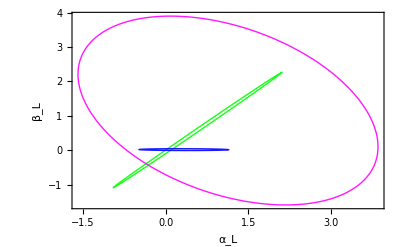
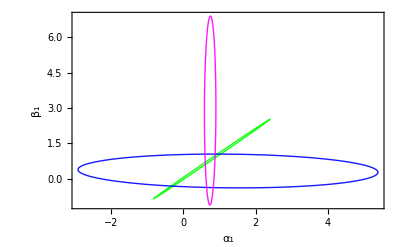
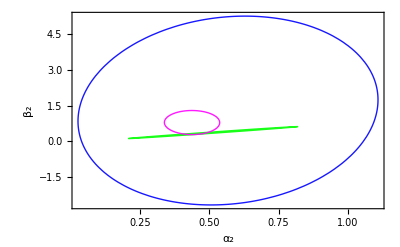
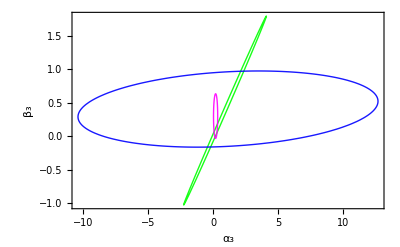
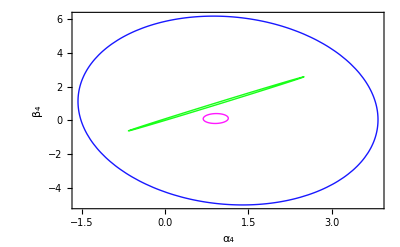
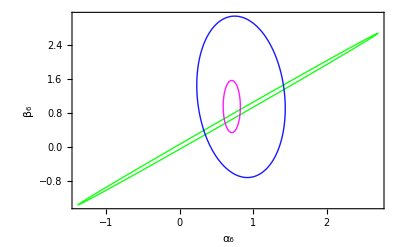
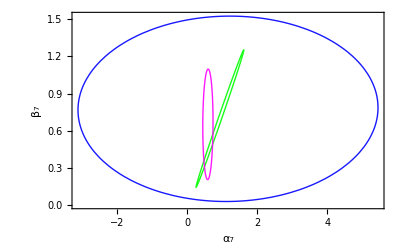
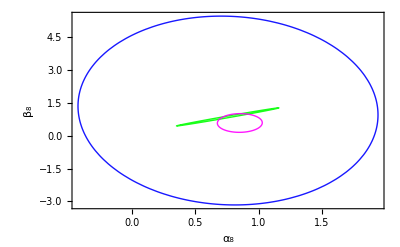

```mathematica
Flatten[Table[
Show[
ListPlot[Transpose@{x[[1,1]],y[[1,1]]},PlotStyle -> Directive[Opacity[0.]]],
Graphics[{Thin,col[[1]],Opacity[.9],EllipsoidQuantile[Transpose@{x[[1,j]],y[[1,j]]},.95] }],
Graphics[{Thin,col[[2]],Opacity[.9],EllipsoidQuantile[Transpose@{x2[[1,j]],y2[[1,j]]},.95]}],
Graphics[{Thin,col[[3]],Opacity[.9],EllipsoidQuantile[Transpose@{x3[[1,j]],y3[[1,j]]},.95]}],
ImageSize-> 400,Frame-> True,PlotRange->All,FrameLabel ->{Style[axes[[j]],FontSize->18],Style[axes[[j+9]],FontSize->18]},
Axes-> False,FrameTicksStyle->Directive[FontSize->17]],
{j,2,9}]]
```